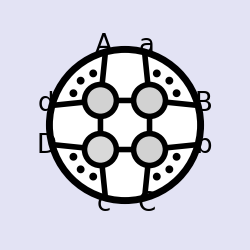
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
n=9;
<<"loop_amplitudes.m";
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c]),
               ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h]};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>Sort[i] Signature[i]Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myexpB=ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3] ab[x,1,y];
cap2expand=ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h];
```

```mathematica
n=9;
source=analyticIntegral[scalarBoxExpansion[n+1,2],False];
c1lvan=Table[If[source[[i,2,1,n+1]]===0,i],{i,Length@source}]//Union;
c2lvan=Table[If[source[[i,2,2,n+1]]===0,i],{i,Length@source}]//Union;
c1landc2lvan=Intersection[c1lvan,c2lvan];
c1nvan=Table[If[source[[i,2,1,n]]===0,i],{i,Length@source}]//Union;
c2nvan=Table[If[source[[i,2,2,n]]===0,i],{i,Length@source}]//Union;
c1nandc2nvan=Intersection[c1nvan,c2nvan];
eitherlnonvan=DeleteCases[Union[c1lvan,c2lvan],Null];
eithernnonvan=DeleteCases[Union[c1nvan,c2nvan],Null];
bothnvan=DeleteCases[Intersection[c1nvan,c2nvan],Null];
bothlnonvan=Complement[Range[Length[source]],eitherlnonvan];
bothnnonvan=Complement[Range[Length[source]],eithernnonvan];
bothnlnonvan=Intersection[bothnnonvan,bothlnonvan];
onlyc1lvan=Complement[c1lvan,c1landc2lvan];
onlyc2lvan=Complement[c2lvan,c1landc2lvan];
onlyc1nvan=Complement[c1nvan,c1nandc2nvan];
onlyc2nvan=Complement[c2nvan,c1nandc2nvan];
```

#### Treatment of data1:

```mathematica
rformoc1lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc1lvan,onlyc2nvan],c1nandc2nvan]]]);
rformoc2lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc2lvan,onlyc1nvan],c1nandc2nvan]]]);
data1=Join[rformoc1lvan,{#[[2]],#[[1]],#[[3]]}&/@rformoc2lvan];
```

```mathematica
premovenl[R[a__,n,n+1],R[b___,cap[{c__},{d_,n,n+1}],e___]]:=
If[Length@{b}>0,(-1)^(Length[{b-1}])premovenl[R[a,n,n+1],R[cap[{c},{d,n,n+1}],b,e]],
With[{ints=Intersection[{c},{b,e}]},
If[(Sort[{a}]===Sort[{c,d}])&&(Length@ints==1),
Times@@{R[First[Complement[{a},{d,b,e}]],b,e],
R[First[Complement[{a},{d,b,e}]],cap[Complement[{a},{d}],Complement[{b,e},ints]],d,n,n+1]
},If[Length[ints]==0,premovenl[R[a,n,n+1],#]&/@sixR[b,cap[{c},{d,n,n+1}],e,First[c]],
R[a,n,n+1]R[b,cap[{c},{d,n,n+1}],e]]
]]];premovenl[R[a__,n,n+1],Except[R[___,cap[{__},{_,n,n+1}],___],R[f___]]]:=R[a,n,n+1]R[f];

movenl[Except[_R,z_]*x_R*y_R]:=z If[ContainsAll[List@@x,{n,n+1}],premovenl[x,y],premovenl[y,x]]
```

```mathematica
cdata1=Select[data1,!StringContainsQ[ToString[#],"Sqrt"]&];
cdata11=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata1,{_,_,-Li[1]}];
cdata12=cdata11[[Complement[Range[Length@cdata11],Flatten[Position[{#[[1]],redR[#[[2]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,#[[3]]}&/@cdata11,{_,0,_}]]]]];
cdata13=cdata12[[Complement[Range[Length@cdata12],First/@Position[{#[[1]],Simplify[Limit[(((freduceR[#[[2]]]//fullabB)/.sortall/.Rtodab/.dabBexp)//fullabB)/._R:>0,e->0]],#[[3]]}&/@cdata12,0]]]];//AbsoluteTiming
cdata14={#[[1]]/.sortcapinR/.{cap[x__,{n-1,n,n+1}]:>cap[x,{1,n-1,n}],cap[x__,{1,n,n+1}]:>cap[x,{1,n-1,n}],cap[{a_,n},{b__,n+1}]:>n}/.cap[{x___,a_,y___},{c___,a_,d___}]:>a,#[[2]]/.R[x___,cap[{n-1,n},___],y___]:>R[x,n-1,y],#[[3]]}&/@cdata13;
cdata15=({If[ SubsetQ[Flatten[List@@(#[[1]]/.cap:>List)],{n,n+1}],premovenl[#[[2]],#[[1]]]/.sortcapinR/.sortR/.toqlog,#[[1]](#[[2]]/.sortcapinR/.sortR/.toqlog)],#[[3]]}&/@cdata14)//.{Qlog[x_/ab[n-1,n,1,cap[{n-2,n-1},y__]]]:>Qlog[x/ab[n-1,n,1,n-2]],Qlog[ab[n-1,n,1,cap[{n-2,n-1},y__]]/x_]:>Qlog[ab[n-1,n,1,n-2]/x],Qlog[x_/ab[n-1,n,1,cap[{1,2},y__]]]:>Qlog[x/ab[n-1,n,1,2]],Qlog[ab[n-1,n,1,cap[{1,2},y__]]/x_]:>Qlog[ab[n-1,n,1,2]/x]};cdata16=cdata15/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]);
```

{47.6037,Null}

#### Treatment of data2:

```mathematica
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={n,n+1},n+2,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};

capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]};
```

```mathematica
data2=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[bothnlnonvan]]);
cdata2=Select[data2,!StringContainsQ[ToString[#],"Sqrt"]&];
cdata21=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata2,{_,_,-Li[1]}]/.sortcapinR;
cdata22=Delete[cdata21,Transpose[List[First/@Position[cdata21,R[cap[{n,n+1},_],n+1,1,2,cap[_,{n-1,n,n+1}]]]]]];
cdata23={#[[1]]#[[2]]/.sortcapinR/.sortR2,#[[3]]}&/@cdata22;
```

replacement rule1

```mathematica
replace1=R[a_,b_,c_,n,n+1]R[cap[{b_,c_},{a_,n,n+1}],c_,d_,n,cap[{n,n+1},{a_,b_,c_}]]:>Which[a===1&&d===n-1,
Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]] dlog[τ],
a===1&&d=!=n-1,
-Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]] dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])],
a=!=1&&d===n-1,
Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))],
a=!=1&&d=!=n-1,(-Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))]+Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]] dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n])/(ab[1,a,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))])]R[a,b,c,d,n];
replace2=R[a_,b_,c_,n,n+1]R[cap[{a_,b_},{c_,n,n+1}],1,a_,n+1,cap[{n,n+1},{a_,b_,c_}]]:>If[c=!=n-1,Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,a,b,c,n]dlog[τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n])],Qlog[ab[1,a,n-1,n]/ab[1,2,n-1,n]] R[1,a,b,c,n]dlog[τ]];
```

```mathematica
(*Union@Flatten@Table[yangcom[R[3,4,5,9,10] R[cap[{4,5},{3,9,10}],6,7,9,cap[{9,10},{3,4,5}]],{i,j},{k,l,m}]+qlogRcom[%564,{i,j},{k,l,m}],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming*)
```

replacement rule2

```mathematica
replace3={R[1,2,3,n,n+1]R[cap[{2,3},{1,n,n+1}],3,a_,b_,cap[{n,n+1},{1,2,3}]]:>-dlog[τ+(-ab[1,2,3,n] ab[3,a,b,n-1]+ab[1,2,3,n-1] ab[3,a,b,n])/(ab[1,3,a,b] ab[2,3,n-1,n])] Qlog[ab[1,2,n-1,n]/ab[1,cap[{2,3},{a,b,1}],n-1,n]] R[1,2,3,a,b],R[c_,d_,n-1,n,n+1]R[cap[{c_,d_},{n-1,n,n+1}],a_,b_,c_,cap[{n,n+1},{c_,d_,n-1}]]:>-Qlog[ab[1,cap[{c,d},{a,b,n-1}],n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n-1]dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] (ab[1,c,d,n-1] ab[a,b,c,n]-ab[1,a,b,c] ab[c,d,n-1,n])))]};
replace4={R[d_,a_,b_,n,n+1] R[cap[{a_,b_},{d_,n,n+1}],b_,c_,n-1,cap[{n,n+1},{d_,a_,b_}]]:>dlog[(τ+(ab[1,2,3,n] (-ab[d,a,c,n-1] ab[d,b,n-1,n]+ab[d,a,n-1,n] ab[d,b,c,n-1]))/(ab[2,3,n-1,n] (-ab[1,d,b,n] ab[d,a,c,n-1]+ab[1,d,a,n] ab[d,b,c,n-1])))/(τ+(ab[1,2,3,n] ab[d,a,n-1,n])/(ab[1,d,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,d]/ab[n-1,n,1,c]] R[d,a,b,c,n-1]+dlog[(τ+(ab[1,2,3,n] ab[d,a,b,n-1] ab[b,c,n-1,n])/(ab[2,3,n-1,n] (ab[1,b,c,n-1] ab[d,a,b,n]-ab[1,d,a,b] ab[b,c,n-1,n])))/(τ+(ab[1,2,3,n] ab[d,a,n-1,n])/(ab[1,d,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,cap[{d,a},{b,c,n-1}]]] R[d,a,b,c,n-1],
R[a_,b_,c_,n,n+1]R[cap[{a_,b_},{c_,n,n+1}],1,2,a_,cap[{n,n+1},{a_,b_,c_}]]:>-R[1,2,a,b,c](dlog[(τ+(ab[1,2,3,n] (ab[1,2,b,c] ab[a,c,n-1,n]-ab[1,2,a,c] ab[b,c,n-1,n]))/((ab[1,2,b,c] ab[1,a,c,n]-ab[1,2,a,c] ab[1,b,c,n]) ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]]+dlog[(τ+(ab[1,2,3,n] (-ab[1,2,a,n] ab[a,b,c,n-1]+ab[1,2,a,n-1] ab[a,b,c,n]))/(ab[1,2,a,n] ab[1,a,b,c] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{b,c},{1,2,a}]]/ab[n-1,n,1,2]]),R[4,5,6,n,n+1]R[cap[{4,5},{6,n,n+1}],2,3,4,cap[{n,n+1},{4,5,6}]]:>Qlog[ab[n-1,n,1,cap[{2,3},{4,5,6}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,4,n] ab[4,5,6,n-1]+ab[2,3,4,n-1] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,4,5,6] ab[2,3,4,n]-ab[1,2,3,4] ab[4,5,6,n])))/(τ+(ab[1,2,3,n]ab[5,6,n-1,n])/(ab[2,3,n-1,n]ab[1,5,6,n]))]+Qlog[ab[n-1,n,1,6]/ab[n-1,n,1,cap[{2,3},{4,5,6}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,5,6] ab[4,6,n-1,n]+ab[2,3,4,6] ab[5,6,n-1,n]))/((ab[1,5,6,n] ab[2,3,4,6]-ab[1,4,6,n] ab[2,3,5,6]) ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n]ab[5,6,n-1,n])/(ab[2,3,n-1,n]ab[1,5,6,n]))],R[2,3,4,n,n+1] R[cap[{3,4},{2,n,n+1}],4,5,6,cap[{n,n+1},{2,3,4}]]:>-Qlog[ab[n-1,n,1,cap[{5,6},{2,3,4}]]/ab[n-1,n,1,2]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,6]-ab[1,2,3,n] ab[2,4,5,6])))/(τ+1)]-Qlog[ab[n-1,n,1,cap[{2,3},{4,5,6}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,4,n] ab[4,5,6,n-1]+ab[2,3,4,n-1] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,4,5,6] ab[2,3,4,n]-ab[1,2,3,4] ab[4,5,6,n])))/(τ+1)]};
replace5={R[c_,d_,n-1,n,n+1] R[cap[{c_,d_},{n-1,n,n+1}],a_,b_,n+1,cap[{n,n+1},{c_,d_,n-1}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[n-1,cap[{c,d},{n-1,n,1}],a,b,n],R[1,a_,b_,n,n+1] R[cap[{a_,b_},{1,n,n+1}],c_,d_,n,cap[{n,n+1},{1,a_,b_}]]:>If[d=!=n-1,-dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,b]] R[1,cap[{a,b},{1,n,n-1}],c,d,n],dlog[τ] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]] R[1,a,b,n-1,n]]};
replace6={R[a_,b_,c_,n,n+1] R[cap[{b_,c_},{a_,n,n+1}],d_,n-1,n,cap[{n,n+1},{a_,b_,c_}]]:>Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] (dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,n-1,n]+dlog[(τ+(ab[1,2,3,n] ab[a,b,c,n-1] ab[a,d,n-1,n])/(ab[2,3,n-1,n] (ab[1,a,c,n] ab[a,b,d,n-1]-ab[1,a,b,n] ab[a,c,d,n-1])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n])/(ab[1,a,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,d,n]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,c,d,n-1,n]-dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n] ab[b,c,n-1,n])/(ab[2,3,n-1,n] (ab[1,a,c,n] ab[b,d,n-1,n]-ab[1,a,b,n] ab[c,d,n-1,n])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[b,c,d,n-1,n]),R[2,3,4,n,n+1]R[cap[{3,4},{2,n,n+1}],5,6,n,cap[{n,n+1},{2,3,4}]]:>-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,3},{5,6,n}]]]dlog[(τ+1)/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]R[2,3,5,6,n]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,4},{5,6,n}]]]R[2,4,5,6,n]dlog[(τ+(ab[1,2,3,n] ab[2,4,n-1,n])/(ab[1,2,4,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,6]-ab[1,2,3,n] ab[2,4,5,6])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,5]]R[2,3,4,5,n]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,n]+ab[2,3,5,n] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,n]-ab[1,2,3,n] ab[2,4,5,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,6,n]+ab[2,3,6,n] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,6,n]-ab[1,2,3,n] ab[2,4,6,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]R[2,3,4,6,n]-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{3,4},{5,6,n}]]]R[3,4,5,6,n]dlog[(τ+(ab[1,2,3,n] (ab[2,4,n-1,n] ab[3,5,6,n]-ab[2,3,n-1,n] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[3,5,6,n]-ab[1,2,3,n] ab[4,5,6,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]};
```

```mathematica
nreplace1=R[c_,d_,e_,n,n+1] R[cap[{c_,d_},{e_,n,n+1}],a_,b_,c_,cap[{n,n+1},{c_,d_,e_}]]:>((-dlog[ab[n,B,e,cap[{a,b},{c,d,e}]]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,d,e}],n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,cap[{a,b},{c,d,e}],c]] Qlog[ab[1,cap[{a,b},{c,d,e}],n-1,n]/ab[1,cap[{d,e},{a,b,c}],n-1,n]]) R[a,b,c,d,e]+(dlog[ab[n,B,d,e]/ab[n,B,c,d]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,c,d]] Qlog[ab[1,d,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]+dlog[ab[n,B,e,cap[{a,b},{c,d,n}]]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,e,n-1,n]]-dlog[ab[n,B,cap[{a,b},{c,d,n}],e]/ab[n,B,c,d]] Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,e,n-1,n]]) R[a,b,c,d,n]+dlog[ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,e,n}],n-1,n]/ab[1,e,n-1,n]] R[a,b,c,e,n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{d,e,n}],n-1,n]/ab[1,e,n-1,n]] R[a,b,d,e,n]+(dlog[ab[n,B,a,b]/ab[n,B,a,c]] Qlog[ab[1,a,n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,a,c]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,c},{d,e,n}],n-1,n]]-dlog[ab[n,B,d,e]/ab[n,B,a,c]] Qlog[ab[1,cap[{a,c},{d,e,n}],n-1,n]/ab[1,e,n-1,n]]) R[a,c,d,e,n]+(dlog[ab[n,B,b,c]/ab[n,B,a,b]] Qlog[ab[1,b,n-1,n]/ab[1,e,n-1,n]]-dlog[ab[n,B,b,c]] Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,e,n}],n-1,n]]+dlog[ab[n,B,d,e]/ab[n,B,b,c]] Qlog[ab[1,cap[{b,c},{d,e,n}],n-1,n]/ab[1,e,n-1,n]]) R[b,c,d,e,n]-dlog[ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],c,d,e,n]/.myexpB)/;a<b<c<d<e;
nreplace2=R[a_,b_,c_,n,n+1] R[cap[{b_,c_},{a_,n,n+1}],d_,e_,n,cap[{n,n+1},{a_,b_,c_}]]:>((dlog[ab[n,B,cap[{d,e},{a,b,c}],a]/ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,e},{a,b,c}],n-1,n]]-dlog[ab[n,B,a,b]] Qlog[ab[1,cap[{d,e},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,e}],n-1,n]]) R[a,b,c,d,e]+(-dlog[(ab[1,c,d,n] ab[n,B,a,d])/(ab[1,a,d,n] ab[n,B,c,d])] Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]+dlog[(ab[1,c,d,n] ab[n,B,a,b])/(ab[1,a,b,n] ab[n,B,c,d])] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]+dlog[ab[n,B,d,c]] Qlog[ab[1,d,n-1,n]/ab[1,cap[{d,c},{a,b,n}],n-1,n]]) R[a,b,c,d,n]+(dlog[(ab[1,c,e,n] ab[n,B,a,e])/(ab[1,a,e,n] ab[n,B,c,e])] Qlog[ab[1,a,n-1,n]/ab[1,e,n-1,n]]-dlog[(ab[1,c,e,n] ab[n,B,a,b])/(ab[1,a,b,n] ab[n,B,c,e])] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,e,n}],n-1,n]]-dlog[ab[n,B,e,c]] Qlog[ab[1,e,n-1,n]/ab[1,cap[{e,c},{a,b,n}],n-1,n]]) R[a,b,c,e,n]+dlog[ab[n,B,c,a]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,e},{c,a,n}],n-1,n]] R[a,c,d,e,n]+(-dlog[ab[n,B,b,a]] Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]+dlog[ab[n,B,cap[{d,e},{b,c,n}],a]] Qlog[ab[1,cap[{d,e},{b,c,n}],n-1,n]/ab[1,a,n-1,n]]) R[b,c,d,e,n]-dlog[ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{1,n-1,n}],c,d,e,n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[cap[{d,e},{1,n-1,n}],a,b,c,n]/.myexpB)/;a<b<c<d<e;
nreplace3=R[cap[{b_,c_},{a_,n,n+1}],c_,d_,ee_,cap[{n,n+1},{a_,b_,c_}]]R[a_,b_,c_,n,n+1]:>(R[a,b,c,d,ee](Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],a]/ab[n,B,a,b]]+Qlog[ab[1,cap[{d,ee},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,ee}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],c]/ab[n,B,a,b]])/.myexpB)/;a<b<c<d<ee;
```

```mathematica
(* no two caps in one R *)
```

```mathematica
Select[(Union@Cases[cdata23,___ R[___]R[___,_cap,___,_cap,___],Infinity])/.replace1/.replace2/.replace3/.replace4/.replace5/.replace6/.nreplace1/.nreplace2/.nreplace3,FreeQ[#,dlog]&]
```

{}

```mathematica
(* one cap *)
```

```mathematica
cdata24=cdata23/.replace1/.replace2/.replace3/.replace4/.replace5/.replace6/.nreplace1/.nreplace2/.nreplace3;First/@Position[cdata24,dlog[_]]//Union//Length
```

102

```mathematica
Length[cdata24]
```

198

```mathematica
(*reptemp1={R[a_,b_,c_,cap[{n,n+1},{d_,ee_,f_}],n+1]R[d_,ee_,f_,n,n+1]:>(
Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,b]]-
Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]R[cap[{a,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,b,c]]+
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,ee]]-
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,f]]+
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,ee,f]]
)/;a≠1&&f≠n-1,R[1,b_,c_,cap[{n,n+1},{d_,ee_,f_}],n+1]R[d_,ee_,f_,n,n+1]:>((
-Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,b,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[1,cap[{b,c},{n-1,n,1}],d,ee,f]dlog[ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,d,f]]-
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,ee,f]]
))/;f≠n-1,
R[a_,b_,c_,cap[{n,n+1},{d_,ee_,n-1}],n+1]R[d_,ee_,n-1,n,n+1]:>
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[a,b,c,n-1,n]dlog[τ/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,b]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]+
R[a,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]
)/;a≠1,
R[1,b_,c_,cap[{n,n+1},{d_,ee_,n-1}],n+1]R[d_,ee_,n-1,n,n+1]:>
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[1,b,c,n-1,n]dlog[τ]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]]-
R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
R[1,b,c,cap[{d,ee},{n-1,n,1}],n-1]dlog[ab[n,B,cap2[{1,b,c},{d,ee,n-1}]]]
)
};
reptemp3=R[a_,b_,c_,n,n+1]:>Which[a≠1&&c≠n-1,dlog[ab[n,B,a,b]/ab[n,B,b,c]]Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]+dlog[ab[n,B,b,c]/ab[n,B,a,c]]Qlog[ab[1,c,n-1,n]/ab[1,a,n-1,n]],
c==n-1&&a≠1,dlog[ab[n,B,a,b]/ab[n,B,n-2,n-1]]Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]],
c!=n-1&&a==1,dlog[ab[n,B,b,c]/ab[n,B,1,2]]Qlog[ab[1,c,n-1,n]/ab[1,b,n-1,n]],
c==n-1&&a==1,dlog[ab[n,B,n-2,n-1]/ab[n,B,1,2]]Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]]];*)
```

```mathematica
replace7={R[1,a_,b_,n,n+1] R[c___,b_,d___,n-1,n,cap[{n,n+1},{1,a_,b_}]]:>Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,c,d]] (dlog[τ] R[1,a,b,n-1,n]-dlog[τ+(ab[1,2,3,n] ab[c,b,d,n-1,n])/(ab[1,c,b,d,n] ab[2,3,n-1,n])] R[1,c,b,d,a,n]-dlog[τ+(ab[1,2,3,n] ab[1,a,b,n-1] ab[c,b,d,n-1,n])/(ab[1,a,b,n] ab[1,c,b,d,n-1] ab[2,3,n-1,n])] R[1,c,b,d,n-1,a]-dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[c,b,d,n-1,n,a]),R[1,d___,a_,e___,n+1,cap[{n,n+1},{a_,b_,n-1}]] R[a_,b_,n-1,n,n+1]:>(-1)^(Length[d])Qlog[ab[n-1,n,1,d,e]/ab[n-1,n,1,b]] (-dlog[τ] R[1,d,e,a,n-1,n]-dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n] ab[1,d,e,a,n-1])/(ab[1,a,b,n-1] ab[2,3,n-1,n] ab[1,d,e,a,n])] R[1,d,e,a,b,n-1]+dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[1,d,e,a,b,n]+dlog[τ+(ab[1,2,3,n] ab[d,e,a,n-1,n])/(ab[2,3,n-1,n] ab[1,d,e,a,n])] R[d,e,a,b,n-1,n])};
replace8={R[1,2,a_,n,n+1] R[a_,b_,c_,n,cap[{n,n+1},{1,2,a_}]]:>-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,b]] R[1,2,a,b,n]+dlog[(τ-(-ab[1,2,3,n] ab[1,a,b,c] ab[2,a,n-1,n]+ab[1,2,3,n] ab[1,a,n-1,n] ab[2,a,b,c])/(ab[1,2,a,n] ab[1,a,b,c] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,a},{1,b,c}]]] R[1,2,a,b,c]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]] R[1,2,a,c,n]-dlog[τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,a]] R[1,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,a]] R[cap[{2,a},{n-1,n,1}],1,b,c,n],R[1,a_,b_,n+1,cap[{n,n+1},{b_,c_,d_}]]R[b_,c_,d_,n,n+1]:>-(-dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,c]] R[1,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] (ab[1,a,b,d] ab[b,c,n-1,n]-ab[1,a,b,c] ab[b,d,n-1,n]))/(ab[1,a,b,n] ab[1,b,c,d] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,cap[{c,d},{1,a,b}]]] R[1,a,b,c,d]+dlog[(τ+(ab[1,2,3,n] ab[b,d,n-1,n])/(ab[1,b,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] R[1,a,b,d,n]-dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,b]] R[1,b,c,d,n]-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,cap[{c,d},{a,b,n}]]] R[a,b,c,d,n]),R[a_,b_,c_,n,n+1] R[c_,d_,n-1,n,cap[{n,n+1},{a_,b_,c_}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[a,b,c,n-1,n]-dlog[(τ-(ab[1,2,3,n] ab[a,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] (-ab[1,b,c,n] ab[a,c,d,n-1]+ab[1,a,c,n] ab[b,c,d,n-1])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,d]/ab[n-1,n,1,cap[{a,b},{c,d,n-1}]]] R[a,b,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{c,d},{a,b,n}]]/ab[n-1,n,1,d]] R[a,b,c,d,n]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] R[a,c,d,n-1,n]-dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,d]] R[b,c,d,n-1,n]};
replace9={R[c_,d_,n-1,n,n+1] R[e_,f_,b_,c_,cap[{n,n+1},{c_,d_,n-1}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[e,f,b,c,n-1]-dlog[(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,f,b}]]/ab[n-1,n,1,d]] R[e,f,b,c,d]+dlog[(τ+(ab[1,2,3,n] ab[e,f,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,f,n-1}]]/ab[n-1,n,1,d]] R[e,f,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[e,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,b,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,b,n-1}]]/ab[n-1,n,1,d]] R[e,b,c,d,n-1]+dlog[(τ+(ab[1,2,3,n] ab[f,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{f,b,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{f,b,n-1}]]/ab[n-1,n,1,d]] R[f,b,c,d,n-1],R[1,a_,b_,n+1,cap[{n,n+1},{c_,d_,n-1}]]R[c_,d_,n-1,n,n+1]:>Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] (-dlog[τ] R[1,a,b,n-1,n]+dlog[τ+(ab[1,2,3,n] ab[1,a,b,n-1] ab[c,d,n-1,n])/(ab[1,a,b,n] ab[1,c,d,n-1] ab[2,3,n-1,n])] R[1,a,b,n-1,cap[{c,d},{n-1,n,1}]]+dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] R[1,a,b,cap[{c,d},{n-1,n,1}],n]+dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[a,b,cap[{c,d},{n-1,n,1}],n-1,n]),R[5,6,n-1,n,n+1]R[1,2,3,4,cap[{n,n+1},{5,6,n-1}]]:>Qlog[ab[n-1,n,1,5]/ab[n-1,n,1,6]] (dlog[τ/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,3,4,n-1]+dlog[(τ+(ab[1,2,3,n-1] ab[5,6,n-1,n])/(ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,3,n-1,cap[{5,6},{n-1,n,1}]]-dlog[(τ+(ab[1,2,3,n] ab[1,2,4,n-1] ab[5,6,n-1,n])/(ab[1,2,4,n] ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,4,n-1,cap[{5,6},{n-1,n,1}]]+dlog[(τ+(ab[1,2,3,n] ab[1,3,4,n-1] ab[5,6,n-1,n])/(ab[1,3,4,n] ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,3,4,n-1,cap[{5,6},{n-1,n,1}]]-dlog[(τ+(ab[1,2,3,n] ab[2,3,4,n-1] ab[5,6,n-1,n])/(ab[2,3,n-1,n] (ab[1,5,6,n-1] ab[2,3,4,n]-ab[1,2,3,4] ab[5,6,n-1,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n])) ]R[2,3,4,n-1,cap[{5,6},{n-1,n,1}]])};
replace10={R[e_,f_,a_,n,n+1]R[a_,b_,c_,n,cap[{n,n+1},{e_,f_,a_}]]:>dlog[(τ+(ab[1,2,3,n] ab[e,a,n-1,n])/(ab[1,e,a,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,e]/ab[n-1,n,1,cap[{e,a},{b,c,n}]]] R[e,a,b,c,n]-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{e,f},{a,b,n}]]/ab[n-1,n,1,b]] R[e,f,a,b,n]+dlog[(τ+(ab[1,2,3,n] (-ab[e,a,b,c] ab[f,a,n-1,n]+ab[e,a,n-1,n] ab[f,a,b,c]))/(ab[2,3,n-1,n] (-ab[1,f,a,n] ab[e,a,b,c]+ab[1,e,a,n] ab[f,a,b,c])))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{e,f},{a,b,c}]]/ab[n-1,n,1,cap[{b,c},{e,f,a}]]] R[e,f,a,b,c]-dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,cap[{e,f},{a,c,n}]]] R[e,f,a,c,n]-dlog[(τ+(ab[1,2,3,n] ab[f,a,n-1,n])/(ab[1,f,a,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,f]/ab[n-1,n,1,cap[{f,a},{b,c,n}]]] R[f,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,c]] R[cap[{b,c},{n-1,n,1}],e,f,a,n],R[1,2,3,n+1,cap[{n,n+1},{4,5,6}]]R[4,5,6,n,n+1]:>+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,3]] (dlog[(τ+(ab[1,2,3,n] ab[4,5,n-1,n])/(ab[1,4,5,n] ab[2,3,n-1,n]))/(τ+1)] R[1,cap[{2,3},{n-1,n,1}],4,5,n]-dlog[(τ+(ab[1,2,3,n] ab[4,6,n-1,n])/(ab[1,4,6,n] ab[2,3,n-1,n]))/(τ+1)] R[1,cap[{2,3},{n-1,n,1}],4,6,n]+dlog[(τ-ab[1,2,3,cap[{n-1,n},{4,5,6}]]/(ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+1)] R[cap[{2,3},{n-1,n,1}],1,4,5,6]-dlog[(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))/(τ+1)] R[cap[{2,3},{n-1,n,1}],1,5,6,n]+dlog[τ+1]R[1,4,5,6,n]),R[4,5,6,n,n+1]R[1,2,3,4,cap[{n,n+1},{4,5,6}]]:>(-dlog[(τ+(ab[1,2,3,n] ab[4,5,n-1,n])/(ab[1,4,5,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{4,5},{1,2,3}]]/ab[n-1,n,1,5]] R[1,2,3,4,5]+dlog[(τ+(ab[1,2,3,n] ab[4,6,n-1,n])/(ab[1,4,6,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{4,6},{1,2,3}]]/ab[n-1,n,1,6]] R[1,2,3,4,6]+dlog[(τ-(ab[1,2,3,n] ab[1,2,4,cap[{5,6},{4,n-1,n}]])/(ab[1,2,4,cap[{5,6},{1,4,n}]] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,4},{1,5,6}]]] R[1,2,4,5,6]-dlog[(τ+(ab[1,2,3,n] ab[1,3,4,cap[{5,6},{4,n-1,n}]])/(ab[1,3,4,n] ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,3]/ab[n-1,n,1,cap[{5,6},{1,3,4}]]] R[1,3,4,5,6]+dlog[(τ+(ab[1,2,3,n] ab[n-1,4,n,cap[{5,6},{2,3,4}]])/(ab[1,4,n,cap[{5,6},{2,3,4}]] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{2,3},{5,6,4}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]] R[2,3,4,5,6]+dlog[(τ+(-ab[1,2,3,n] ab[4,5,6,n-1]+ab[1,2,3,n-1] ab[4,5,6,n])/(ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,3]] R[cap[{2,3},{n-1,n,1}],1,4,5,6])};
```

```mathematica
nreplace4=R[a_,b_,c_,n+1,cap[{n,n+1},{d_,ee_,f_}]]R[d_,ee_,f_,n,n+1]:>(-(Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,b]]-Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]R[cap[{a,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,c]]+Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,b,c]]+Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,ee]]-Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,f]]+Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,ee,f]]))/.myexpB;
nreplace5=R[1,a_,b_,n+1,cap[{n,n+1},{a_,b_,c_}]]R[cap[{a_,b_},{1,n,n+1}],b_,c_,n,n+1]:>(If[c≠n-1,dlog[ab[n,B,b,c]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,a,b,cap[{b,c},{n-1,n,1}],n],Qlog[ab[1,b,n-1,n]/ab[1,2,n-1,n]] dlog[τ] R[1,a,b,n-1,n]]/.myexpB)/;c==b+1==a+2;
nreplace6=R[1,a_,b_,c_,cap[{n,n+1},{c_,d_,e_}]] R[c_,d_,e_,n,n+1]:>(((dlog[ab[n,B,c,d]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,c,n-1,n]]+dlog[ab[n,B,d,e]/ab[n,B,c,e]] Qlog[ab[1,e,n-1,n]/ab[1,c,n-1,n]]) R[1,a,b,c,n]+dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,a,b,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,a,c,cap[{c,d},{n-1,n,1}],n]+dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{c,e},{n-1,n,1}],n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,b,c,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{1,a,b},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[1,cap[{a,b},{n-1,n,1}],c,d,e]+dlog[ab[n,B,cap2[{1,a,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{a,c},{n-1,n,1}],c,d,e]-dlog[ab[n,B,cap2[{1,b,c},{c,d,e}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{b,c},{n-1,n,1}],c,d,e]+dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+(dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]) R[cap[{a,b},{n-1,n,1}],c,d,e,n]+(-dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]) R[cap[{a,c},{n-1,n,1}],c,d,e,n]+(dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]) R[cap[{b,c},{n-1,n,1}],c,d,e,n])/.myexpB)/;a<b<c<d<e;
nreplace7=R[1,a_,b_,c_,cap[{n,n+1},{d_,e_,f_}]] R[d_,e_,f_,n,n+1]:>(((dlog[ab[n,B,d,e]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]]+dlog[ab[n,B,e,f]/ab[n,B,d,f]] Qlog[ab[1,f,n-1,n]/ab[1,d,n-1,n]]) R[1,a,b,c,n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,a,b,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,a,b,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,a,c,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,a,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,b,c,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,b,c,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{1,a,b},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[1,cap[{a,b},{n-1,n,1}],d,e,f]+dlog[ab[n,B,cap2[{1,a,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{a,c},{n-1,n,1}],d,e,f]-dlog[ab[n,B,cap2[{1,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{b,c},{n-1,n,1}],d,e,f]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[a,b,c,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[a,b,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],d,e,f,n]-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[cap[{a,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[cap[{b,c},{n-1,n,1}],d,e,f,n])/.myexpB)/;a<b<c<d<e<f&&f≠n-1;
nreplace8=R[a_,b_,c_,d_,cap[{n,n+1},{e_,f_,n-1}]] R[e_,f_,n-1,n,n+1]:>((dlog[ab[n,B,e,f]/ab[n,B,f,n-1]] Qlog[ab[1,f,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,d,n]+Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] (-dlog[τ/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[a,b,c,n-1,n]+dlog[τ/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[a,b,d,n-1,n]-dlog[τ/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[a,c,d,n-1,n]+dlog[τ/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[b,c,d,n-1,n]-dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,c,n]+dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,d,n]+dlog[ab[n,B,cap2[{a,b,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,n-1,n]-dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,c,d,n]+dlog[ab[n,B,cap2[{a,b,c},{e,f,n-1}]]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,c,n-1,n]+dlog[ab[n,B,cap2[{a,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,d,n-1,n]+dlog[ab[n,B,e,f]/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,c,d,n]+dlog[ab[n,B,cap2[{b,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,c,n-1,n]+dlog[ab[n,B,cap2[{a,b,d},{e,f,n-1}]]/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,d,n-1,n]+dlog[ab[n,B,cap2[{b,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],c,d,n-1,n]))/.myexpB)/;a≠1&&a<b<c<d<e<f;
nreplace9=R[1,a_,b_,c_,cap[{9,10},{d_,e_,8}]] R[d_,e_,8,9,10]:>(dlog[ab[n,B,d,e]/ab[n,B,e,n-1]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]] R[1,a,b,c,n]-dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,n-1,n]-dlog[ab[n,B,cap2[{1,a,b},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n-1]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]+dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,n-1,n]+dlog[ab[n,B,cap2[{1,a,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n-1]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]-dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,n-1,n]-dlog[ab[n,B,cap2[{1,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n-1]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[τ/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,n-1,n]-dlog[ab[n,B,d,e]/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,cap[{d,e},{n-1,n,1}],n-1,n]+dlog[1/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,c,cap[{d,e},{n-1,n,1}],n-1,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[b,c,cap[{d,e},{n-1,n,1}],n-1,n]/.myexpB)/;a<b<c<d<e;
nreplace10=R[a_,b_,c_,d_,cap[{n,n+1},{d_,e_,f_}]] R[d_,e_,f_,n,n+1]:>((dlog[ab[n,B,d,e]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n]+dlog[ab[n,B,e,f]/ab[n,B,d,f]] Qlog[ab[1,f,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n]+Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] (-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,e]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,d,e]] R[a,b,d,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,d,e]] R[a,c,d,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,d,e]] R[b,c,d,cap[{d,e},{n-1,n,1}],n])+Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] (dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,f]] R[a,b,c,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,d,f]] R[a,b,d,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,d,f]] R[a,c,d,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,d,f]] R[b,c,d,cap[{d,f},{n-1,n,1}],n])+Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] (-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,e,f]] R[a,b,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,e,f]] R[a,b,d,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,e,f]] R[a,c,d,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,e,f]] R[b,c,d,cap[{e,f},{n-1,n,1}],n])+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,cap2[{a,c,d},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[cap[{a,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,cap2[{a,b,d},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]] R[cap[{a,d},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[cap[{b,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,cap2[{b,c,d},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]] R[cap[{b,d},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,cap2[{a,c,d},{d,e,f}]]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[cap[{c,d},{n-1,n,1}],d,e,f,n])/.myexpB)/;a<b<c<d<e<f;
```

```mathematica
(* no R[___,cap,___] R[___] *)
```

```mathematica
Select[(Union[Cases[cdata24,___ R[___]R[___,_cap,___],Infinity]/.-x_:>x])/.replace7/.replace8/.replace9/.replace10/.nreplace4/.nreplace5/.nreplace6/.nreplace7/.nreplace8/.nreplace9/.nreplace10,FreeQ[#,dlog]&]
```

{}

```mathematica
cdata25=cdata24/.replace7/.replace8/.replace9/.replace10/.nreplace4/.nreplace5/.nreplace6/.nreplace7/.nreplace8/.nreplace9/.nreplace10;
```

```mathematica
Length[cdata25]
```

198

```mathematica
First/@Position[cdata25,dlog[_]]//Union//Length
```

198

```mathematica
cdata26=cdata25;
```

#### Treatment of data3:

```mathematica
(* data3 *)
```

```mathematica
data3=Select[If[ContainsAll[List@@#[[1]],{n,n+1}],{#[[2]],#[[1]],#[[3]]},#]&/@(Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[bothlnonvan,bothnlnonvan],bothnvan]]]),!StringContainsQ[ToString[#],"Sqrt"]&];cdata3=Select[data3,!StringContainsQ[ToString[#],"Sqrt"]&];cdata31=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata3,{_,_,-Li[1]}];cdata32={(#[[1]])/.{R[m___,cap[{n+1,1},a__],b___]:>R[m,cap[{n,1},a],b]}/.sortcapinR/.{R[x___,cap[a__,{1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y],R[x___,cap[a__,{n-1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y]}/.sortcapinR/.R[x___,cap[{___,a_,___},{___,a_,___}],y___]:>R[x,a,y]/.sortall/.R[x___,n+1]:>R[x,n],(#[[2]]/.sortall/.sortcapinR)/.{R[m___,cap[{1,n+1},a__],b___]:>R[m,1,b]}/.R[m___,cap[{n-2,n-1},a__],b___]:>R[m,n-2,b]/.R[x___,cap[a__,{b__,n+1}],y___]:>R[x,cap[a,{b,n}],y],#[[3]]}&/@cdata31;
cdata33=DeleteCases[{#[[1]]((#[[2]]/.sortR/.toqlog)/.i_R:>0)//.{Qlog[x_/ab[n-1,n,1,cap[{n-2,n-1},y__]]]:>Qlog[x/ab[n-1,n,1,n-2]],Qlog[ab[n-1,n,1,cap[{n-2,n-1},y__]]/x_]:>Qlog[ab[n-1,n,1,n-2]/x],Qlog[x_/ab[n-1,n,1,cap[{1,2},y__]]]:>Qlog[x/ab[n-1,n,1,2]],Qlog[ab[n-1,n,1,cap[{1,2},y__]]/x_]:>Qlog[ab[n-1,n,1,2]/x]}/.Qlog[ab[n-1,n,1,i_]/ab[n-1,n,1,j_]] R[1,i_,j_,n-1,n]:>0,#[[3]]}&/@cdata32,{0,_}];cdata34=cdata33/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]);
```

```mathematica
(*The collection of cdata 16, cdata26 and cdata 34, then take the limit of e to 0*)
```

```mathematica
cdataall={#[[1]],(#[[2]]/.Li[1]:>Li[1]/2//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e^a_ b_]:>a log[e]+log[b]}/.{log[x_]:>log[If[x===e,e,Normal[Series[x,{e,0,0}]]]],Li[x_]:>Li[Limit[x,e->0]]}}&/@Join[cdata16,cdata26,cdata34];
```

```mathematica
(* tree , data43 has dropped the divergence of log[e]*)
amp1=Total[(rAmp[n+1,2]/.Join[Table[i->i-1,{i,2,n+1}],{1->n+1}]/.Join[Table[i->i-1,{i,2,n+1}],{1->n+1}])/.sortR/.toqlog/.R[x___]R[y___]:>0/.{R[x___,cap[{n+1,1},{b__,n}],y___]:>R[x,n,y]}/.R[x___,cap[a__,{1,n+1,n}],y___]:>R[x,cap[a,{n,n-1,1}],y]/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab)/.sortcapinR/.sortR2]/.R[cap[{a___,x_,b___},{c___,x_,d___}],z___]:>R[x,z]/.sortR2/. Qlog[ab[n-1,n,1,b_]/ab[n-1,n,1,a_]] R[cap[{a_,b_},{1,n-1,n}],c___,a_,d___]:>Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,cap[{a,b},{c,d}]]] R[b,c,a,d]//Simplify;
etreen2=Total[DeleteCases[DeleteCases[scalarBoxRatioExpansion[n+1,2]/.onShellGraph[x__][y__]:>0,0]/.i_scalarBox:>First[Flatten[analyticIntegral[i,False]]],amp[n+1,2]Li[1]]]//Simplify;
data4={amp1,(((etreen2/.{Li[1]:>Li[1]/2})//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0)/.amp[n+1,2]->1};
data41=Flatten[Outer[List,List@@amp1,List@@Expand[etreen2/.{Li[1]:>Li[1]/2}/.amp[n+1,2]->1],1],1];
data42={#[[1]],(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data41;
data43={#[[1]]/.dlog[x_]:>dlog[x/.sortall],(#[[2]]//twistorSimplify)/.sortall}&/@data42;
```

```mathematica
(* easy 4 massbox for any n*)
easy4massbox=Flatten[With[{n=9},Table[{dlog[τ] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{b-1,b},{c-1,c,n}]]] R[b-1,b,c-1,c,n],Li[1]-Li[1]-Li[1-(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n])]-1/2 (log[(ab[1,2,n-1,n] ab[1,n-2,n-1,n] ab[b-1,b,c-1,c])/(ab[1,2,n-2,n-1] ab[1,c-1,c,n] ab[b-1,b,n-1,n])]+2log[e]) log[(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n])]},{b,3,n-4},{c,b+2,n-2}]],1];
data5={#[[1]]//dabRcanel,((#[[2]])//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@easy4massbox;
```

```mathematica
(*Check log[e] divergent vanishing*)
randomPositiveZs[20]
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
logediv=cdataall[[All,1]].D[cdataall[[All,2]],log[e]]+2 amp1 log[(τ ab[1,2,3,n] ab[n-3,n-2,n-1,n])/((1+τ) (τ ab[1,n-3,n-2,n] ab[2,3,n-1,n]+ab[1,2,3,n] ab[n-3,n-2,n-1,n]))]+(D[easy4massbox[[All,2]],log[e]]. easy4massbox[[All,1]]);
```

```mathematica
((logediv/.sortab/.qlogtodab//neabp)//todoubleab//todmatrix//fuse)/.dabne[{8,9}]/.DmatrixEval3[{3,3,3},3]/.log->Log/.dlog[x_]:>D[Log[x],τ]//neabp;
Limit[Integrate[%,τ],τ->0]-Limit[Integrate[%,τ],τ->Infinity]//FullSimplify
```

0

```mathematica
Do[
If[Union[#]=={0},Print[i," ",j];,Print["error|",i,j]]&@With[{hh=((logediv/.sortab/.qlogtodab//neabp)//todoubleab//todmatrix//fuse)/.dabne[{i,j}]},
Flatten@ParallelTable[temp=Integrate[Collect[Expand[((hh/.DmatrixEval3[{a,b,c},3]//neabp//Simplify)/.Log->log)//expandlog],_log]/.log->Log/.dlog[x_]:>D[Log[x],τ]//Simplify,τ];FullSimplify[Limit[temp,τ->0]-Limit[temp,τ->Infinity]],{a,2},{b,a,2},{c,b,2}]],{i,2},{j,i+1,2}]
```

$Aborted

```mathematica
(* Divergent part of the second term *)
```

```mathematica
secpart={FirstCase[#,_R,Infinity],#/FirstCase[#,_R,Infinity]}&/@Flatten[scalarBoxExpansion[n,1]/.onShellGraph[x_][y__]:>rForm[onShellGraph[x][y]]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]]];
secpart=(R[2,n-2,n-1,n,n+1]/.toqlog/.{ab[X,1,2]:>1,ab[X,7,8]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab))(Total[Times@@#&/@(DeleteCases[secpart,{_,-Li[1]|Li[1]}]/.{Li[1]->Li[1]/2})]+Total@DeleteCases[(DeleteCases[scalarBoxRatioExpansion[n,1]/.onShellGraph[x_][y__]:>0,0]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]])/amp[n,1],Li[1]]Total[rAmp[n,1]]);
data6={secpart[[1;;2]]#[[1]],#[[2]]}&/@(Reverse[List@@Collect[#,_R]]&/@(List@@(secpart[[3]])));
```

```mathematica
(*(*coefficents of 1/τ in hard4massbox*)
hardlogt={{Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]] R[1,2,4,5,7]dlog[τ/(τ+1)],-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]},
{Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]] R[1,2,3,4,7]dlog[τ/(τ+1)],-Li[1-(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]-1/2(log[τ]+log[(ab[1,2,3,4]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[3,4,7,8])])log[(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]},
{ Qlog[ab[n-1,n,1,cap[{2,3},{4,5,7}]]/ab[n-1,n,1,6]] R[2,3,4,5,7]dlog[τ/(τ+1)],-Li[1-(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[2,3,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[2,3,6,7]ab[4,5,7,8])])log[(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]}}; *)
(*divergent part of hardbox @ tau-> 0 for any n *)
hardlogt=With[{n=9},Join[Table[{R[1,2,b-1,b,n-1]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,n-2]]dlog[τ/(τ+1)],-Li[1-(ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])]-1/2(log[τ]+log[(ab[1,2,b-1,b]ab[1,n-2,n-1,n]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])])log[(ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])]},{b,4,n-3}],Flatten[Table[{Qlog[ab[n-1,n,1,cap[{a-1,a},{b-1,b,n-1}]]/ab[n-1,n,1,n-2]] R[a-1,a,b-1,b,n-1]dlog[τ/(τ+1)],-Li[1-(ab[a-1,a,n-1,n]ab[b-1,b,n-2,n-1])/(ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])]-1/2(log[τ]+log[(ab[a-1,a,b-1,b]ab[1,n-2,n-1,n]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])])log[(ab[a-1,a,n-1,n]ab[b-1,b,n-2,n-1])/(ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])]},{a,3,n-5},{b,a+2,n-3}],1]]
];
(*divergent part of hardbox @ tau-> infnity for any n *)
hardloginf=With[{n=9},Join[Table[{-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,n-2]] R[1,b-1,b,n-2,n-1]dlog[τ+1],-Li[1-(ab[1,2,b-1,b] ab[1,n-2,n-1,n])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n])]-1/2 log[(ab[1,2,b-1,b] ab[1,n-2,n-1,n])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n])] (log[(ab[1,2,3,n] ab[1,2,n-1,n] ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n] ab[2,3,n-1,n])]-log[τ])},{b,4,n-3}],Flatten[Table[{Qlog[ab[n-1,n,1,cap[{c-1,c},{1,b-1,b}]]/ab[n-1,n,1,2]] R[1,b-1,b,c-1,c]dlog[τ+1],-Li[1-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])]-1/2 log[(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])](log[(ab[1,2,3,n] ab[1,2,n-1,n] ab[b-1,b,c-1,c])/(ab[1,2,c-1,c] ab[1,b-1,b,n] ab[2,3,n-1,n])]-log[τ])},{b,4,n-4},{c,b+2,n-2}],1]]];
```

```mathematica
(*(* coefficients of 1/τ *)
temp1=(Limit[#,τ->0]&/@(τ#[[1]]&/@data13)).(Last/@data13);
temp2=Limit[#[[1]]τ,τ->0]&/@data28;
(* Position[temp22,Indeterminate]//Flatten *)
(* {18,31,40} *)
temp2=ReplacePart[temp2,{18->(SeriesCoefficient[τ data27[[18,1]],{τ,0,0}]/.sortall/.{R[1,2,3,6,7]->sixR[1,2,3,6,7,8]}/.sortall//dabRcanel)/.sortall,
31->(SeriesCoefficient[τ data27[[31,1]],{τ,0,0}]/.sortall/.{R[2,3,6,7,8]->sixR[2,3,6,7,8,4]})/.sortall//Simplify//dabRcanel,
40->(SeriesCoefficient[τ data27[[40,1]],{τ,0,0}]/.sortall/.{R[3,4,5,6,7]->sixR[3,4,5,6,7,8]}/.sortall//dabRcanel)/.sortall}].(Last/@data28);
temp3=((Limit[#,τ->0]&/@(τ#[[1]]&/@data33))/.dab[x___,cap[a__,{b___,9,c___}],y___]:>dab[x,cap[a,{b,8,c}],y]).(Last/@data33);
temp4=Limit[τ data4[[1]],τ->0](Last@data4);
tempeasy=(Limit[τ #[[1]],τ->0]&/@data5).data5[[All,2]];
temphard=(Limit[τ #[[1]],τ->0]&/@hardlogt).hardlogt[[All,2]];
tempsec=Limit[τ secpart,τ->0]//dabRcanel;*)
```

```mathematica
(*(* check 1/tau and log[tau]/tau *)
minideg[f_,var_]:=minideg[f,var]=If[SeriesCoefficient[f,{var,0,0}]===0,minideg[D[f,var],var]+1,0]
tempall=(temp1+temp2+temp3+temp4+tempeasy+temphard-tempsec)/.{log[x_]:>(log[0]minideg[x,τ]+log[SeriesCoefficient[x,{τ,0,minideg[x,τ]}]])}/.Li[x_]:>Li[Limit[x,τ->0]]/.{log[1]->0,Li[0]->0};*)
```

```mathematica
(*Table[numtemp=(((tempall//neab1)//todoubleab//todmatrix//fuse)/.dabne[{1,2}]/.DmatrixEval3[{3,i,j},3])//neab1;
(numtemp/.{log[0]->0}/.log->Log/.Li[x_]:>PolyLog[2,x])//FullSimplify,{i,1,8},{j,1,i}]*)
```

```mathematica
(*(* log e num check *)
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];

data12=({#[[1]]#[[2]],#[[3]]}&/@data12);
data32=({#[[1]]#[[2]],#[[3]]}&/@data32);
logedata1=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data12];
logedata2=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data25];
logedata2=logedata2/.{R[x___,cap[{y__},{7,8,9}],z___]:>R[x,cap[{y},{n-1,n,1}],z],R[x___,cap[{y__},{1,8,9}],z___]:>R[x,cap[{y},{n-1,n,1}],z]}/.R[x___,cap[{y__},{a_,8,9}],z___]:>R[x,cap[{y},{a,8,B}],z];
logedata3=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data32];
treeresult=2 *amp2  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))];
loge4massbox=Total[Total[{#[[1]]logecoeff[#[[2]]//fullabB]}&/@easy4massbox]];*)
```

```mathematica
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];
randomPositiveZs[20]
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧]
```

```mathematica
(*echeck=cdata16[[All,1]].((cdata16[[All,2]]//fullabB)//logecoeff)+cdata26[[All,1]].((cdata26[[All,2]]//fullabB)//logecoeff)+cdata34[[All,1]].((cdata34[[All,2]]//fullabB)//logecoeff)+2 *amp1  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]+easy4massbox[[All,1]].((easy4massbox[[All,2]]//fullabB)//logecoeff);*)
```

```mathematica
(*Do[
If[Union[#]=={0},Print[i," ",j];,Print["error|",i,j]]&@With[{hh=((echeck/.sortab/.qlogtodab//neabp)//todoubleab//todmatrix//fuse)/.dabne[{1,3}]},
Flatten@ParallelTable[temp=Integrate[Collect[Expand[((hh/.DmatrixEval3[{a,b,c},3]//neabp//Simplify)/.Log->log)//expandlog],_log]/.log->Log/.dlog[x_]:>D[Log[x],τ]//Simplify,τ];FullSimplify[Limit[temp,τ->0]-Limit[temp,τ->Infinity]],{a,2},{b,a,2},{c,b,2}]],{i,2},{j,i+1,2}]*)
```

```mathematica
cdata12345=<<"cdata12345";
dlogtaupart=DeleteCases[Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))],{0,_}]/.{Li[x_]:>Li[x]-Li[Limit[x,τ->0]]}/.Li[0]->0/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},Which[hh===0,log[τ]log[y/jj]+log[x/τ]log[y]-log[Limit[x/τ,τ->0]]log[jj],jj===0,log[τ]log[x/hh]+log[y/τ]log[x]-log[Limit[y/τ,τ->0]]log[hh],True,log[x]log[y]-log[hh]log[jj]]]/.log[1]->0;
ndlogtaupart=Join[{},{#[[1]]/.dlog[τ]:>0,#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]})];
pdlogtaupart={#[[1]]dlog[τ+1],#[[2]]}&/@DeleteCases[Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))],{0,_}]/.{Li[x_]:>Li[Limit[x,τ->0]]}/.Li[0]->0/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},Which[hh===0,log[τ]log[jj]+log[Limit[x/τ,τ->0]]log[jj],jj===0,log[τ]log[hh]+log[Limit[y/τ,τ->0]]log[hh],True,log[hh]log[jj]]]/.log[1]->0;
```

```mathematica
substract1=(Join[{dlog[τ]#[[1]],#[[2]]}&/@DeleteCases[dlogtaupart,{0,_}|{_,0}],DeleteCases[ndlogtaupart,{0,_}|{_,0}],hardloginf]/.log[1]->0);
substract2=substract1/.dlog[x_]:>If[Limit[1/x//neab1,τ->+Infinity]===0,dlog[x/(τ+1)],dlog[x]]/.dlog[1]->0;
substract3=Join[substract1/.dlog[x_]:>If[Limit[1/x//neab1,τ->+Infinity]===0,dlog[τ+1],0]/.dlog[1]->0,pdlogtaupart];
substract5=({#[[1]],#[[2]]/.log[x_]:>logmonic[Factor[x]]/.log[1]->0/.log[1/x_]:>-log[x]/.{log[(τ+x_)/(τ+y_)]:>0,log[τ/(τ+z_)]:>0}}/.{Li[x_]:>Li[Limit[x,τ->Infinity]]}/.Li[0]->0)&/@substract3;
substract4=Table[{substract3[[i,1]],substract3[[i,2]]-substract5[[i,2]]},{i,Length@substract3}];
substract7=substract5/.{log[τ+x_]:>log[τ]};
substract6=Table[{substract5[[i,1]],Simplify[substract5[[i,2]]-substract7[[i,2]]]},{i,Length@substract5}];
subsecpart=secpart/.dlog[(τ+(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]))/τ]->dlog[(τ+(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]))/(τ+1)];
```

```mathematica
finiteint=DeleteCases[Join[substract2,substract4,substract6],{0,_}|{_,0}];(* and subsecpart*)
divint=DeleteCases[substract7,{0,_}|{_,0}];
```

```mathematica
mysim[exp_]:=(exp//Simplify)/.{log[x_]-log[y_]:>log[x/y],log[x_]+log[y_]:>log[x y],log[x_]log[y_]-log[z_]log[w_]:>0/;((x z===1&&y w ===1)||(x w===1&&y z ===1))}/.log[1]->0
trivialint=Select[finiteint,FreeQ[#[[2]],τ]&];
ntrivialint=DeleteCases[FixedPoint[mysim,Complement[finiteint,trivialint]/.log[x_]:>logmonic[x]/.{log[1]->0,log[1/x_]:>-log[x]}],{_,0}];//AbsoluteTiming
```

{38.2725,Null}

```mathematica
ntrivialint1=Select[ntrivialint,FreeQ[#[[2]],Li]&];
ntrivialint2=Select[ntrivialint,!FreeQ[#[[2]],Li]&];
ntrivialint21=DeleteCases[ntrivialint2/.dlog[x__]:>dlog[x/.sortab]/.dlog[1]:>0,{0,_}];
ntrivialint3=Select[ntrivialint1,Head[Expand[#[[2]]]]===Times&];
ntrivialint4=Complement[ntrivialint1,ntrivialint3];
ntrivialint5=Cases[ntrivialint3,{dlog[x_] y_,a_ log[b_]log[c_]}/;FreeQ[c,τ]];
ntrivialint6=Complement[ntrivialint3,ntrivialint5];
```

```mathematica
Join[ntrivialint2,ntrivialint4,ntrivialint6]//Length
```

939

```mathematica
ntrivialint5=ntrivialint5/.{dlog[x_] y_,a_ log[b_]log[c_]}/;FreeQ[c,τ]:>{ y,a log[c]int[x,b]};
ntrivialint5//Length
```

415

```mathematica
ntrivialint51=ntrivialint5/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y]);
ntrivialint52=ntrivialint51/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]Limit[x,τ->0]]/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]};
```

```mathematica
ntrivialint6=ntrivialint6/.{dlog[x_] y_,a_ log[b_]log[c_]}:>{ y,a int[x,b,c]};
```

```mathematica
int2[exp_]:=exp/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y])/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]}/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]/Limit[x,τ->0]];
int23[exp_]:=(((exp/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y])/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]}/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]/Limit[x,τ->0]])/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]})//int2)/.int[a___,1/x_,b___]:>-int[a,x,b]/.{int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-a b}]-Li[{2},{1-a c}]+Li[{2},{1-c}]-Li[{2},{1-b}],int[(τ+a_)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-a }]-Li[{2},{1-a c}]+Li[{2},{1-c}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ)]:>Li[{2},{1-a b}]-Li[{2},{1-a }]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ)]:>Li[{2},{1-a }],int[τ/(1+τ),τ/(1+τ),1+τ]:>-Zeta[3],int[τ/(1+τ),1+τ,(1+τ)/τ]:>Zeta[3],int[τ/(1+τ),1+τ a_,τ/(1+τ a_)]:>2Li[{3},{1-a}]+Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])-2Zeta[3],int[1+τ,τ+a_,τ/(τ+a_)]:>2Li[{3},{1-a}]+Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])-2Zeta[3],int[τ/(1+τ),τ/(1+τ a_),(1+τ)/(1+τ a_)]:>-Li[{3},{1-a}]-2Li[{3},{a}]+log[a](2Li[{2},{a}]+log[1-a]log[a])+2Zeta[3],int[1+τ,τ/(1+τ),1+τ]:>-Zeta[3],int[τ+1,τ/(τ+a_),(1+τ)/(τ+a_)]:>-Li[{3},{1-a}]-Li[{3},{a}]+1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])+Zeta[3],int[1+τ,1+τ,(τ+a_)/(1+τ)]:>-Li[{3},{1-a}],int[(τ+a_)/(τ+1),1+τ,τ/(1+τ)]:>-2Li[{3},{1-a}]-Li[{3},{a}]-1/2 log[1-a] log[a]^2+Zeta[3],int[(τ+a_)/(τ+1),1+τ,(τ+a_)/(1+τ)]:>Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[a]log[1-a])-Zeta[3],int[(τ+a_)/(τ+1),τ/(τ+a_),(1+τ)/(τ+a_)]:>-Li[{3},{a}]+Zeta[2]log[a]-1/2 log[1-a] log[a]^2+Zeta[3]}/.{int[(τ+a_)/(τ+1),τ+a_,τ/(τ+a_)]:>-2Li[{3},{1-a}]-Li[{3},{a}]-log[a](Li[{2},{1-a}]+1/2 log[1-a]log[a])+Zeta[3],int[τ/(1+τ),τ/(1+τ a_),(1+τ b_)/(1+τ a_)]:>G[1,a]G[0,0,b]-G[0,b]G[1,0,a]-G[1,a]G[1,0,b]+G[0,b]G[1,b,a]+2G[1,0,0,a]-G[1,0,0,b]+2G[1,1,0,a]-G[1,b,0,a],int[1+τ,τ+a_,(τ+ b_)/(τ+a_)]:>-(G[1,a]G[0,0,b]-G[0,b]G[1,0,a]-G[1,a]G[1,0,b]+G[0,b]G[1,b,a]+2G[1,0,0,a]-G[1,0,0,b]+2G[1,1,0,a]-G[1,b,0,a]),int[1+τ,τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[1,a](G[0,0,b]-G[1,0,b])+G[0,b](G[1,b,a]-G[1,0,a])+G[1,0,0,a]+2G[1,1,0,a]-G[1,b,0,a],int[(τ+a_)/(1+τ),τ+a_,(τ+b_)/(τ+a_)]:>-2Zeta[2]G[1,a]-Zeta[2]G[1,b/a]+2Zeta[2]G[1/a,b/a]-G[1/a,b/a]G[0,0,a]-G[1/a,b/a]G[1,0,a]+G[0,a](G[1,0,b/a]-G[1/a,0,b/a]-Zeta[2])+G[1,0,0,a]+2G[1,1,0,a]+G[1,1,0,b/a]-G[1/a,1,0,b/a]-Zeta[3],int[(τ+a_)/(1+τ),τ/(τ+b_),(τ+a_)/(τ+b_)]:>-Zeta[2]G[1,b/a]+G[1/a,b/a]G[1,0,a]-2G[0,a]G[1/a,1/a,b/a]+G[1,0,0,b/a]+G[1,1,0,b/a]-G[1/a,0,0,b/a]+G[1/a,1,0,b/a]-2G[1/a,1/a,0,b/a],int[(τ+a_)/(1+τ),1+τ,(τ+b_)/(1+τ)]:>-2Zeta[2]G[1,a]+Zeta[2]G[1,b]-G[a,b]G[1,0,a]-G[0,1,0,a]-G[1,0,0,a]+2G[1,1,0,a]-G[1,1,0,b]+G[a,1,0,b]-Zeta[3],int[(τ+a_)/(τ+1),τ+b_,τ/(τ+b_)]:>-2Zeta[2]G[1,b]+G[a,b](2Zeta[2]+G[0,0,a])+2G[0,a]G[a,a,b]+G[1,0,0,b]+2G[1,1,0,b]-G[a,0,0,b]-2G[a,a,0,b],int[(τ+a_)/(1+τ),τ/(τ+b_),(1+τ)/(τ+b_)]:>Zeta[2]G[1,b]+G[a,b](-2Zeta[2]-G[0,0,a]+G[1,0,a])-2G[0,a]G[a,a,b]-G[1,0,0,b]-G[1,1,0,b]+G[a,0,0,b]-G[a,1,0,b]+2G[a,a,0,b],int[(τ+a_)/(1+τ),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 π^2 G[0,a]-1/6 π^2 G[b,a]-G[1,a] G[0,0,b]+G[1,a] G[1,0,b]+G[0,b] (-π^2/6+G[0,b,a]+G[1,0,a]-G[1,b,a]-G[b,b,a])-G[0,b,0,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,b,0,a]+Zeta[3],int[(τ+a_)/(τ+1),τ+b_,(τ+a_)/(τ+b_)]:>Zeta[2]G[a,b]+G[1,b]G[0,0,a]-G[1,b]G[1,0,a]+G[0,a](Zeta[2]-G[1,0,b]+G[1,a,b]+G[a,0,b]+G[a,a,b])-G[1,0,0,a]+2G[1,0,0,b]+2G[1,1,0,b]-G[1,a,0,b]-2G[a,0,0,b]-G[a,a,0,b]-Zeta[3],
int[(τ+b_)/(1+τ),τ+a_,(τ+c_)/(τ+a_)]:>-G[b,c] G[0,0,b]+G[1,a] G[0,0,c]-G[0,c] G[1,0,a]-G[1,a] G[1,0,c]+G[0,c] G[1,c,a]+G[0,c] G[b,0,a]+G[b,a] (G[0,0,b]-G[0,0,c]+G[b,0,c])+G[0,b] (-G[b,a] G[b,c]+2 G[b,b,a])-G[0,c] G[b,c,a]+2 G[1,0,0,a]-G[1,0,0,c]+2 G[1,1,0,a]-G[1,c,0,a]-2 G[b,0,0,a]+G[b,0,0,c]-2 G[b,b,0,a]+G[b,c,0,a],
int[(τ+b_)/(1+τ),τ/(τ+a_),(τ+c_)/(τ+a_)]:>G[b,a] G[0,0,c]+G[0,c] G[1,0,a]+G[1,a] (-G[0,0,c]+G[1,0,c])-G[0,c] G[1,c,a]-G[0,c] G[b,0,a]-G[b,a] G[b,0,c]+G[0,b] (G[b,a] G[b,c]-2 G[b,b,a])+G[0,c] G[b,c,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,c,0,a]+G[b,0,0,a]+2 G[b,b,0,a]-G[b,c,0,a]
}
```

```mathematica
ntrivialint61=((ntrivialint6/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]})//int2)//int23;
```

```mathematica
ntrivialint41=mysim[Collect[#,_int]]&/@(({#[[1]]/._dlog->1,Expand[#[[2]] FirstCase[#[[1]],_dlog]]/.{a_ log[b_]log[c_]dlog[d_]:>a int[d,b,c]}}&/@ntrivialint4)/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}//.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ],
int[a_,b_]:>int[a]log[b]/;FreeQ[b,τ]});
ntrivialint42=(ntrivialint41//int23)/.{int[τ/(1+τ),(1+a_ τ)/(1+τ)]:>Li[{2},{(-1+a)/a}]+1/2 log[a]^2};
```

```mathematica
(Cases[ntrivialint42/.{int[τ/(1+τ),τ,1+τ a_]:>Li[{3},{a}]-Li[{2},{a}]log[a]-1/2 log[1-a] log[a]^2,int[τ/(1+τ),1+τ,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]+Li[{3},{a}]-Zeta[2]log[a]+Li[{2},{1-a}]log[a]+1/2 log[1-a] log[a]^2-Zeta[3],int[τ/(1+τ),1+τ a_,1+τ a_]:>2Zeta[3]-2Li[{3},{1-a}],int[τ/(1+τ),1+τ a_,(1+τ b_)/(1+τ a_)]:>G[1,a](G[1,0,b]-G[0,0,b])+G[0,b](G[1,0,a]-G[1,b,a])-G[1,0,0,a]-2G[1,1,0,a]+G[1,b,0,a],int[τ/(1+τ),(1+τ)/(1+τ a_),(1+τ b_)/(1+τ a_)]:>-Zeta[2]G[1,a]+G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[1+τ,(1+τ)/(τ+a_),(τ+b_)/(τ+a_)]:>Zeta[2](G[1,b]-G[1,a])+G[1,b](G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[τ/(τ+1),(1+τ b_)/(1+τ a_),(1+τ c_)/(1+τ a_)]:>-G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] (π^2/3+G[0,0,b]+G[0,0,c]-G[1,0,b]-G[1,0,c])+G[1,b] (-(π^2/3)-G[0,0,c]+G[1,0,c])+G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b],
int[1+τ,(τ+b_)/(τ+a_),(τ+c_)/(τ+a_)]:>-G[0,b] G[1,0,a]+G[1,a] (G[0,0,b]-G[1,0,b])+G[1,c] (G[0,0,a]-G[0,0,b]-G[1,0,a]+G[1,0,b])-G[0,a] G[1,0,c]+G[0,b] G[1,0,c]+G[0,a] G[1,a,c]+G[0,b] G[1,b,a]-G[0,b] G[1,b,c]+G[1,0,0,a]+2 G[1,1,0,a]-G[1,a,0,c]-G[1,b,0,a]+G[1,b,0,c]},_int,Infinity]//Union)
```

{}

```mathematica
mma2maple[exp_]:=CForm[exp];
maple2mma[str_]:=ToExpression[StringReplace[StringReplace[StringReplace[str,Shortest["zeta["~~x__~~"]"]:>"Zeta["~~x~~"]"],{Shortest["ln("~~x__~~")"]:>"log["~~x~~"]","Mpl"->"Li","["->"{","]"->"}"}],{Shortest["Li({"~~x__~~"})"]:>"Li[{"~~x~~"}]"}]]
maple2mma["(1/2)*ln(1/a)^2+Mpl([2], [(-1+a)/a])"]
```

Li[{2},{(-1+a)/a}]+1/2 log[1/a]^2

```mathematica
logmonic[exp_]:=log[Expand[Numerator[exp]/(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])] ]+log[(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])];
monic[exp_]:={Expand[Numerator[exp]/(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])] ,(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])};
antimonic[exp_]:={Expand[Numerator[exp]/(First[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(First[DeleteCases[CoefficientList[Denominator[exp],τ],0]])], (First[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/First[DeleteCases[CoefficientList[Denominator[exp],τ],0]])};
int[a___,{b___},c___]:=Total[int[a,#,c]&/@{b}]
int[___,1,___]:=0;tocap1[exp_]:=exp/.ab[cap[{3,4},{a_,7,8}],2,7,8]:>ab[2,a,7,8] ab[3,4,7,8]/.ab[x___,cap[a_,b_],y___]:>If[a∩b=!={},ab[x,cap[a,b],y]//.capexpand/.sortab,ab[x,cap[a,b],y]]//.{1-(ab[1,3,7,8] ab[2,3,b__])/(ab[1,3,b__] ab[2,3,7,8]):>ab[3,cap1[{1,2},{b},{7,8}]]/(ab[1,3,b] ab[2,3,7,8]),(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,5,6]-ab[1,2,3,8] ab[2,4,5,6])):>(ab[1,2,3,8] ab[2,cap1[{3,4},{5,6},{7,8}]])/(ab[2,3,7,8] ab[2,cap1[{3,4},{5,6},{1,8}]]),(ab[1,2,3,8] (ab[2,3,7,8] ab[2,4,6,7]-ab[2,3,6,7] ab[2,4,7,8]))/(ab[2,3,7,8] (-ab[1,2,4,8] ab[2,3,6,7]+ab[1,2,3,8] ab[2,4,6,7])):>(ab[1,2,3,8] ab[2,6,7,8] ab[2,3,4,7])/(ab[2,3,7,8] ab[2,cap1[{3,4},{6,7},{1,8}]]),(ab[1,2,3,8] ab[2,3,4,7] ab[2,6,7,8])/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,6,7]-ab[1,2,3,8] ab[2,4,6,7])):>(ab[1,2,3,8] ab[2,6,7,8] ab[2,3,4,7])/(ab[2,3,7,8] ab[2,cap1[{3,4},{6,7},{1,8}]]),ab[1,2,5,8] ab[2,4,6,7]-ab[1,2,4,8] ab[2,5,6,7]:>ab[2,cap1[{4,5},{6,7},{1,8}]]}/.ab[x___,cap[a_,b_],y___]:>If[a∩{x,y}=!={},ab[x,cap[a,b],y]//.capexpand/.sortab,ab[x,cap[a,b],y]]/.{ab[1,c_,a_,8] ab[b_,a_,d__]-ab[1,b_,a_,8] ab[c_,a_,d__]:>ab[a,cap1[{b,c},{d},{1,8}]],ab[1,a_,c_,8] ab[b_,d__,8]-ab[1,a_,b_,8] ab[c_,d__,8]:>ab[8,cap1[{1,a},{b,c},{d}]],-ab[a__,b_,e_] ab[b_,c__,d_]+ab[a__,b_,d_] ab[b_,c__,e_]:>ab[b,cap1[{a},{c},{d,e}]],-ab[b_,a_,e__] ab[c_,a_,d__]+ab[b_,a_,d__] ab[c_,a_,e__]:>ab[4,cap1[{b,c},{d},{e}]],ab[d_,a_,c__] ab[b__,a_,e_]-ab[d_,b__,a_] ab[a_,c__,e_]:>ab[a,cap1[{b},{c},{d,e}]],ab[1,a_,d_,8] ab[a_,b_,c__]-ab[1,a_,b_,8] ab[a_,d_,c__]:>ab[a,cap1[{b,d},{c},{1,8}]],-ab[2,3,7,8] ab[2,4,b_,8]+ab[2,3,b_,8] ab[2,4,7,8]:>ab[2,b,7,8] ab[2,3,4,8]}/.{(ab[1,2,3,8] ab[cap[{1,2},{5,6,7}],cap[{6,7},{1,2,5}],7,8])/((-ab[1,2,5,7] ab[1,2,6,8]+ab[1,2,5,6] ab[1,2,7,8]) ab[1,5,6,7] ab[2,3,7,8]):>-(ab[1,2,3,8] ab[1,2,5,7] ab[5,6,7,8])/(ab[1,2,5,8] ab[1,5,6,7] ab[2,3,7,8]),(ab[1,2,3,8] (-ab[2,3,5,6] ab[4,6,7,8]+ab[2,3,4,6] ab[5,6,7,8]))/((ab[1,5,6,8] ab[2,3,4,6]-ab[1,4,6,8] ab[2,3,5,6]) ab[2,3,7,8]):>(ab[6,cap1[{2,3},{4,5},{7,8}]] ab[1,2,3,8])/(ab[6,cap1[{2,3},{4,5},{1,8}]] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,2,4,5] ab[3,5,7,8]-ab[1,2,3,5] ab[4,5,7,8]))/((ab[1,2,4,5] ab[1,3,5,8]-ab[1,2,3,5] ab[1,4,5,8]) ab[2,3,7,8]):>(ab[1,2,3,8] ab[5,cap1[{1,2},{3,4},{7,8}]])/(ab[2,3,7,8] ab[5,cap1[{1,2},{3,4},{1,8}]]),-ab[3,4,7,8] ab[3,5,6,7]+ab[3,4,6,7] ab[3,5,7,8]:>ab[3,6,7,8] ab[3,4,5,7],(ab[1,2,3,5] ab[3,4,7,8]-ab[1,2,3,4] ab[3,5,7,8])/(ab[1,3,4,5] ab[2,3,7,8]):>ab[3,cap1[{1,2},{4,5},{7,8}]]/(ab[1,3,4,5] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,2,b_,6] ab[a_,6,7,8]-ab[1,2,a_,6] ab[b_,6,7,8]))/((ab[1,2,b_,6] ab[1,a_,6,8]-ab[1,2,a_,6] ab[1,b_,6,8]) ab[2,3,7,8]):>(ab[6,cap1[{1,2},{a,b},{7,8}]] ab[1,2,3,8])/(ab[1,2,6,8] ab[1,a,b,6] ab[2,3,7,8]),(ab[1,2,3,6] ab[3,a_,7,8]-ab[1,2,3,a_] ab[3,6,7,8])/(ab[1,3,a_,6] ab[2,3,7,8]):>ab[3,cap1[{1,2},{a,6},{7,8}]]/(ab[1,3,a,6] ab[2,3,7,8]),(ab[1,2,3,8] (ab[2,4,7,8] ab[3,5,6,8]-ab[2,3,7,8] ab[4,5,6,8]))/(ab[8,cap1[{1,2},{3,4},{5,6}]] ab[2,3,7,8]):>(ab[1,2,3,8] ab[8,cap1[{3,4},{5,6},{7,2}]])/(ab[8,cap1[{1,2},{3,4},{5,6}]] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,3,4,6] ab[4,5,7,8]-ab[1,3,4,5] ab[4,6,7,8]))/(ab[1,3,4,8] ab[1,4,5,6] ab[2,3,7,8]):>(ab[1,2,3,8] ab[4,cap1[{1,3},{5,6},{7,8}]])/(ab[1,3,4,8] ab[1,4,5,6] ab[2,3,7,8]),(ab[1,2,3,8] ab[2,3,4,8] ab[2,6,7,8])/(ab[2,cap1[{3,4},{6,8},{1,8}]] ab[2,3,7,8]):>(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]),(-ab[1,2,3,8] ab[4,5,6,7]+ab[1,2,3,7] ab[4,5,6,8])/(ab[1,4,5,6] ab[2,3,7,8]):>ab[1,2,3,cap[{8,7},{4,5,6}]]/(ab[1,4,5,6] ab[2,3,7,8]),(ab[1,2,3,8] ab[2,3,4,7] ab[5,6,7,8])/(ab[2,3,7,8] (ab[1,5,6,7] ab[2,3,4,8]-ab[1,2,3,4] ab[5,6,7,8])):>(ab[1,2,3,8] ab[2,3,4,7] ab[5,6,7,8])/(ab[2,3,7,8] ab[2,3,4,cap[{8,1},{5,6,7}]])}/.ab[x___,cap[{a__},{y___,d_,z___}],m___,d_,n___]:>neab[ab[x,cap[{a},{y,d,z}],m,d,n]/ab[d,cap1[{a},{y,z},{x,m,n}]]] ab[d,cap1[{a},{y,z},{x,m,n}]];
```

```mathematica
log[((τ ab[1,4,5,8] ab[2,3,7,8]+ab[1,2,3,8] ab[4,5,7,8]) ab[5,6,7,8])/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.log[x_]:>logmonic[Factor[x]]
```

log[(ab[1,4,5,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[4,5,7,8])]+log[(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]

```mathematica
Li[(τ ab[2,3,7,8] (ab[1,5,6,8] ab[4,5,7,8]-ab[1,4,5,8] ab[5,6,7,8]))/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.Li[x_]:>Li[1+antimonic[Factor[x-1]]]
```

Li[{1+(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))/(1+(τ ab[1,5,6,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[5,6,7,8])),0}]

```mathematica
maple2mma["ln(1/a)*zeta[2]+(1/2)*ln(1/a)^3-zeta[3]-Mpl([3],[(a-1)/a])+Mpl([2,1],[a/(a-1),(a-1)/a])-2*Mpl([1,2],[1,(a-1)/a])-2*Mpl([2,1],[1,(a-1)/a])"]
```

{-3 Zeta-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+2 Zeta log[1/a]+1/2 log[1/a]^3}

```mathematica
{-3 Zeta-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+2 Zeta log[1/a]+1/2 log[1/a]^3}/.Zeta:>0
```

{-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+1/2 log[1/a]^3}

```mathematica
(1+(τ ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8]))/(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))
```

(1+(τ ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8]))/(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))

```mathematica
(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])-(ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8])//Together
```

(ab[2,3,7,8] (-ab[1,4,5,8] ab[3,4,7,8]+ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,2,3,8] ab[3,4,7,8] ab[4,5,7,8])

```mathematica
ntrivialintli1={If[FreeQ[#[[2]],τ],#[[1]]/.dlog[x__]:>-log[x/.τ:>0],#[[1]]],#[[2]]}&/@(ntrivialint21/.log[__]:>0);ntrivialintli2=DeleteCases[{If[FreeQ[#[[2]],τ],0,#[[1]]],#[[2]]}&/@(ntrivialint21/.log[__]:>0),{0,_}];
ntrivialintli21=ntrivialintli2[[First/@Position[ntrivialintli2,dlog[1+τ]]]];ntrivialintli22=ntrivialintli2[[Union[First/@Position[ntrivialintli2,dlog[τ/(τ+1)]]]]];ntrivialintli23=Complement[Complement[ntrivialintli2,ntrivialintli21],ntrivialintli22];
```

```mathematica
ntrivialintli21done=({#[[1]]/.i_dlog:>1,intli[1+τ,#[[2]]//Simplify]}&/@ntrivialintli21)/.(τ c_)/(τ a_+d_):>τ/(τ+d/a)(Expand[c/a])/.intli[x__,-y__]:>-intli[x,y]/.{intli[1+τ,Li[1/(1+τ)]]:>Zeta[3],intli[1+τ,-Li[1]+Li[τ/(1+τ)]]:>-2Zeta[3],intli[1+τ,Li[1]-Li[1-a_/(1+τ)]]:>2Li[{3},{a}]-log[a]Li[{2},{a}],intli[1+τ,Li[a_/(1+τ)]]:>Li[{3},{a}],intli[1+τ,Li[a_/(τ b_+c_)]]:>log[c/b]Li[{2},(a/b)/(-1+(c/b))]-G[0,-1+c/b,c/b,a/b],intli[1+τ,-Li[a_]+Li[(τ a_)/(τ+b_)]]:>G[0,b]G[0,1,a]-G[0,b]G[0,1-b,a]-G[0,1,1,a]+G[0,1-b,1,a],intli[1+τ,Li[1-a_]-Li[((1-a_)τ)/(a_+τ)]]:>Li[{3},{1-a}]+Li[{2},{1-a}]log[a]+1/2 log[a]^2 log[1-a]+Li[{3},{a}]-Zeta[3]-Zeta[2]log[a]}/.{intli[1+τ,Li[1-a_]-Li[((1-a_)τ)/(b_+τ)]]:>G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])+G[0,a](-G[1,0,b]+G[1,a,b])+G[1,1,0,b]-G[1,a,0,b],intli[1+τ,Li[1-a_]-Li[1-(τ a_)/(τ+b_)]]:>-Zeta[2]G[1,b]+G[1-a,b](Zeta[2]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1-a,0,b]+G[1,1,0,b]-G[1-a,1,0,b]}/.Li[1-x_]:>Li[1-Times@@monic[x]]/;!FreeQ[x,τ]/.{intli[1+τ,Li[1-a_]-Li[1-((1+τ)a_)/(τ+b_)]]:>G[1,a](Zeta[2]+G[0,0,b]-G[1,0,b])+G[0,b](-G[1,0,a]+G[1,b,a])+G[1,1,0,a]-G[1,b,0,a],intli[1+τ,Li[1-a_]-Li[1-((τ+c_) a_)/(τ+b_)]]:>-(1/6) π^2 G[1,b]+1/6 π^2 G[(-1+a+b)/a,c]+G[0,a] G[0,b] G[(-1+a+b)/a,c]+1/6 G[1-a,b] (π^2-6 G[1,0,a])-G[(-1+a+b)/a,c] G[1,0,a]-G[0,a] G[1,0,b]-G[(-1+a+b)/a,c] G[1,0,b]+G[0,a] G[1-a,0,b]+G[0,b] G[(-1+a+b)/a,b,c]+G[0,a] G[(-1+a+b)/a,b/a,c]-G[0,b] G[(-1+a+b)/a,b/a,c]+G[1,1,0,b]-G[1-a,1,0,b]+G[(-1+a+b)/a,1,0,c]-G[(-1+a+b)/a,b,0,c]+G[(-1+a+b)/a,b/a,0,c]};
```

```mathematica
ntrivialintli21done[[9]]
```

```mathematica
{Qlog[ab[n-1,n,1,6]/ab[n-1,n,1,4]] R[1,2,3,4,8],G[0,-1+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,4,5,8] ab[3,4,7,8]-ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,3,4,8] ab[1,4,5,8] ab[2,3,7,8])]-Li[{2},(ab[1,2,3,8] (ab[1,4,5,8] ab[3,4,7,8]-ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,3,4,8] ab[1,4,5,8] ab[2,3,7,8] (-1+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])))] log[(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])]}
```

```mathematica
signli[exp_]:=exp/.{Li[x___]:>0/;!FreeQ[x,τ],Li[x___]:>1/;FreeQ[x,τ]};
```

```mathematica
ntrivialintli22done
```

{{Qlog[ab[7,8,1,4]/ab[7,8,1,6]] R[1,2,3,4,7],-G[0,(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])] G[1,(ab[1,4,5,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[4,5,7,8]),(ab[3,4,7,8] ab[4,5,6,7])/(ab[3,4,6,7] ab[4,5,7,8])]+10+G[(1-(ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))/(1-(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])),(ab[1,4,5,8] ab[1])/(ab[1,3,4,8] ab[1]),0,(ab[3,4,7,8] ab[4,5,6,7])/(ab[3,4,6,7] ab[4,5,7,8])]},44,{1}}
 |  |  |  |

```mathematica
ntrivialint23done
```

{1}
 |  |  |  |

```mathematica
partdlog[x_]:=With[{hh=Cases[Collect[x[[1]],_dlog],_dlog,Infinity]},If[Length@hh>1,{#,x[[2]]}&/@(# D[x[[1]],#]&/@hh),{x}]]
ntrivialint22=Flatten[partdlog/@ntrivialint21,1];
```

```mathematica
ntrivialint2withoutLi11=(((({#[[1]]/._dlog->1,Expand[#[[2]] FirstCase[#[[1]],_dlog]]/.{a_ log[b_]log[c_]dlog[d_]:>a int[d,b,c]}}&/@DeleteCases[ntrivialint22/._Li:>0,{_,0}]))/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]}));
ntrivialint2withoutLi12=int2[(Collect[(ntrivialint2withoutLi11//Expand//Simplify)/.int[τ/(τ+1),y_]:>int[τ/(τ+1)]log[y]/;FreeQ[{y},τ],int[τ/(τ+1)]]//Simplify)//.log[x_]+log[y_]:>log[x y]/.log[1]:>0];
```

```mathematica
ntrivialint2withoutLi13=(ntrivialint2withoutLi12/.{(ab[1,2,3,8] ab[cap[{2,3},{4,5,8}],2,7,8])/(ab[1,cap[{2,3},{4,5,8}],2,8] ab[2,3,7,8]):>1,(ab[1,2,3,8] ab[cap[{5,6},{2,3,8}],6,7,8])/(ab[1,cap[{5,6},{2,3,8}],6,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,6,7}],3,7,8])/(ab[1,cap[{3,4},{5,6,7}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{4,5},{6,7,8}],4,7,8])/(ab[1,cap[{4,5},{6,7,8}],4,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,6,8}],3,7,8])/(ab[1,cap[{3,4},{5,6,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,7,8}],3,7,8])/(ab[1,cap[{3,4},{5,7,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{6,7,8}],3,7,8])/(ab[1,cap[{3,4},{6,7,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])}/.log[1]:>0//.int[a___,(1+τ)/b_,c___]:>-int[a,b/(1+τ),c]//int23)/.{
int[(τ+b_)/(τ+a_),(1+τ c_)/(1+τ d_)]:>-Li[{2},{1-a c}]+Li[{2},{1-b c}]+Li[{2},{1-a d}]-Li[{2},{1-b d}],
int[(τ+a_)/(τ+b_),(1+τ c_)]:>Li[{2},{1-a c}]-Li[{2},{1-b c}],
int[(τ+a_)/(τ+b_),(1+τ c_)/(1+τ)]:>-Li[{2},{1-a}]+Li[{2},{1-b}]+Li[{2},{1-a c}]-Li[{2},{1-b c}],
int[(τ+a_)/(τ+b_),τ/(1+τ c_)]:>-Li[{2},{1-a c}]+Li[{2},{1-b c}]-Log[a]^2/2+Log[b]^2/2,
int[(τ+a_)/(τ+b_),(1+τ )]:>Li[{2},{1-a}]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-a b}]-Li[{2},{1-a c}]+Li[{2},{1-c}]-Li[{2},{1-b}],int[(τ+a_)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-a }]-Li[{2},{1-a c}]+Li[{2},{1-c}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ)]:>Li[{2},{1-a b}]-Li[{2},{1-a }]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ)]:>Li[{2},{1-a }],int[(τ)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-c}]-Li[{2},{1-b}],
int[(τ)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-c}],
int[(τ)/(τ+1),(1+τ b_)/(1+τ )]:>-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ b_)]:>Li[{2},{1-a b}]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),1/(1+τ c_)]:>-Li[{2},{1-a c}]+Li[{2},{1-c}],int[τ/(τ+1),τ,1+τ a_]:>Li[{3},{a}]-log[a]Li[{2},{a}]-1/2 log[a]^2 log[1-a],int[τ/(1+τ),τ,(1+τ a_)/(1+τ)]:>Li[{3},{a}]-log[a]Li[{2},{a}]-1/2 log[a]^2 log[1-a]-Zeta[3]
}/.Li[_,{0}]:>0;
```

```mathematica
ntrivialint2withoutLi14=ntrivialint2withoutLi13/.int[x_,y__]:>int[tocap1[x],y]/.(ab[1,2,3,8] ab[cap[{2,3},{4,5,8}],2,7,8])/(ab[1,cap[{2,3},{4,5,8}],2,8] ab[2,3,7,8]):>1/.log[1]:>0/.{int[(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8]+τ ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8])/(ab[1,4,5,6] (τ ab[1,2,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[2,4,7,8])),(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[2,3,5,6] (τ ab[1,3,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[3,4,7,8])),(ab[1,2,3,4] (τ ab[1,4,5,8] ab[2,3,7,8]+ab[1,2,3,8] ab[4,5,7,8]))/(ab[1,2,4,5] (τ ab[1,3,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[3,4,7,8]))]:>log[(ab[1,4,5,6] ab[2,4,7,8])/ab[4,cap1[{1,2},{5,6},{7,8}]]]log[(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[1,3,4,8] ab[2,3,5,6] ab[2,3,7,8])]log[(ab[1,2,3,4] ab[1,4,5,8])/(ab[1,2,4,5] ab[1,3,4,8])]+int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]))]log[(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[1,3,4,8] ab[2,3,5,6] ab[2,3,7,8])]-int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])]log[(ab[1,2,3,4] ab[1,4,5,8])/(ab[1,2,4,5] ab[1,3,4,8])]-int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]))]};
ntrivialint2withoutLi2=ntrivialint2withoutLi14/.{int[τ/(1+τ),1+τ,τ/(1+τ)]:>-Zeta[3],int[τ/(1+τ),τ,1+τ a_]:>Li[{3},{a}]-Li[{2},{a}]log[a]-1/2 log[1-a] log[a]^2,int[τ/(1+τ),1+τ,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]+Li[{3},{a}]-Zeta[2]log[a]+Li[{2},{1-a}]log[a]+1/2 log[1-a] log[a]^2-Zeta[3],int[τ/(1+τ),1+τ a_,1+τ a_]:>2Zeta[3]-2Li[{3},{1-a}],
int[τ/(τ+1),τ/(1+τ a_),(1+τ a_)/(1+τ)]:>Li[{3},{1-a}]+2 Li[{3},{a}]-1/6 π^2 Log[a]-Li[{2},{1-1/a}] Log[a]-Li[{2},{a}] Log[a]-Log[a]^3/2-2 Zeta[3],
int[τ/(τ+1),1+τ a_,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]-Li[{3},{a}]+1/6 π^2 Log[a]-Li[{2},{1-a}] Log[a]-1/2 Log[1-a] Log[a]^2+Zeta[3],int[τ/(1+τ),τ,(1+τ a_)/(1+τ b_)]:>Li[{3},{a}]-Li[{3},{b}]-Li[{2},{a}] Log[a]-1/2 Log[1-a] Log[a]^2+Li[{2},{b}] Log[b]+1/2 Log[1-b] Log[b]^2,int[τ/(1+τ),1+τ a_,(1+τ b_)/(1+τ a_)]:>G[1,a](G[1,0,b]-G[0,0,b])+G[0,b](G[1,0,a]-G[1,b,a])-G[1,0,0,a]-2G[1,1,0,a]+G[1,b,0,a],int[τ/(1+τ),(1+τ)/(1+τ a_),(1+τ b_)/(1+τ a_)]:>-Zeta[2]G[1,a]+G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[τ/(1+τ),(1+τ a_)/(1+τ),(1+τ b_)/(1+τ a_)]:>1/6 π^2 G[1,a]-G[1,b] (π^2/6+G[0,0,a]-G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[1,0,0,a]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]}/.{int[τ+1,τ/(τ+a_),(a_+τ)/(τ+1)]:>-(-Li[{3},{1-a}]-Li[{3},{a}]+1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])+Zeta[3]),int[(τ+a_)/(τ+1),τ/(τ+b_),τ+b_]:>-1/3 π^2 G[1,b]+G[a,b] (π^2/3+G[0,0,a])+2 G[0,a] G[a,a,b]+G[1,0,0,b]+2 G[1,1,0,b]-G[a,0,0,b]-2 G[a,a,0,b],int[τ+1,(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,a]-G[1,b] (π^2/6+G[0,0,a]-G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[1,0,0,a]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]}/.{int[(τ+a_)/(τ+b_),τ+c_]:>Li[{2},{1-a/c}]-Li[{2},{1-b/c}]-Log[a/b] Log[c],int[(τ+a_)/(τ+b_),(τ+c_)/(τ+d_)]:>Li[{2},{1-a/c}]-Li[{2},{1-b/c}]-Li[{2},{1-a/d}]+Li[{2},{1-b/d}]-Log[a/b] Log[c/d]};
```

```mathematica
ntrivialint2withoutLi3=ntrivialint2withoutLi2/.{int[x_,1/(τ+a_),y_]:>-int[x,τ+a,y],int[x_,y_,1/(τ+a_)]:>-int[x,τ+a,y],int[(τ+1)/(τ+a_),y__]:>-int[(τ+a)/(τ+1),y]}/.{int[(τ+a_)/(τ+1),τ+1,τ/(τ+1)]:>Li[{3},{1-1/a}]-Li[{3},{1-a}]-1/6 π^2 log[a]-log[a]^3/6,int[(τ+a_)/(τ+1),τ+a_,τ/(τ+a_)]:>(Li[{2},{a}]Log[a]+1/2 Log[a]^2 Log[1-a]-Li[{3},{a}]-2Li[{3},{1-a}]-Zeta[2]Log[a]+Zeta[3]),int[(τ+a_)/(1+τ),1+τ,(τ+a_)/(1+τ)]:>Li[{3},{a}]-Li[{2},{a}] log[a]-1/2 log[1-a] log[a]^2-Zeta[3]}/.{int[(τ+a_)/(τ+1),τ+1,(τ+b_)/(1+τ)]:>-1/3 π^2 G[1,a]+1/6 π^2 G[1,b]-G[a,b] G[1,0,a]-G[0,1,0,a]-G[1,0,0,a]+2 G[1,1,0,a]-G[1,1,0,b]+G[a,1,0,b]-Zeta[3],
int[(τ+b_)/(τ+1),τ+a_,τ/(τ+a_)]:>-1/3 π^2 G[1,a]+G[b,a] (π^2/3+G[0,0,b])+2 G[0,b] G[b,b,a]+G[1,0,0,a]+2 G[1,1,0,a]-G[b,0,0,a]-2 G[b,b,0,a],int[(τ+b_)/(τ+1),τ+a_,(τ+b_)/(τ+a_)]:>1/6 π^2 G[b,a]+G[1,a] G[0,0,b]-G[1,a] G[1,0,b]+G[0,b] (π^2/6-G[1,0,a]+G[1,b,a]+G[b,0,a]+G[b,b,a])+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-2 G[b,0,0,a]-G[b,b,0,a]-Zeta[3],int[(τ+b_)/(τ+1),τ/(τ+a_),(τ+a_)/(1+τ)]:>-1/6 π^2 G[1,a]+G[b,a] (π^2/3+G[0,0,b]-G[1,0,b])+2 G[0,b] G[b,b,a]+G[1,0,0,a]+G[1,1,0,a]-G[b,0,0,a]+G[b,1,0,a]-2 G[b,b,0,a],int[(τ+b_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[b,a] (-π^2/6+G[0,0,b])+G[0,b] G[1,0,a]+G[1,a] (-G[0,0,b]+G[1,0,b])-G[0,b] G[1,b,a]-G[0,b] G[b,0,a]-G[0,b] G[b,b,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,0,0,a]+G[b,b,0,a],int[(τ+a_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 π^2 G[0,a]-1/6 π^2 G[b,a]-G[1,a] G[0,0,b]+G[1,a] G[1,0,b]+G[0,b] (-π^2/6+G[0,b,a]+G[1,0,a]-G[1,b,a]-G[b,b,a])-G[0,b,0,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,b,0,a]+Zeta[3],int[(τ+a_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]+1/6 π^2 G[b,a]+G[b,a] G[0,0,b]-G[b,a] G[1,0,b]+G[0,b] (π^2/6-G[0,0,a]+G[b,b,a])+2 G[0,0,0,a]+G[0,0,0,b]-G[0,1,0,b]+G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,b]-G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a],int[(τ+b_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/3 π^2 G[1,b]+1/6 π^2 G[b,a]+G[1,a] (π^2/6+G[0,0,b]-G[1,0,b])-G[b,a] G[1,0,b]+G[0,b] (π^2/6-G[1,0,a]+G[1,b,a]+G[b,0,a]+G[b,b,a])-G[0,1,0,b]+2 G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,a]+2 G[1,1,0,b]-G[1,b,0,a]-2 G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a]-Zeta[3]}/.{int[(τ+c_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[c,a] G[0,0,b]+G[0,b] G[1,0,a]+G[1,a] (-G[0,0,b]+G[1,0,b])-G[0,b] G[1,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a],int[(τ+c_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[0,b] G[1,0,a]+G[1,a] (π^2/6+G[0,0,b]-G[1,0,b])-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[0,b] G[1,b,a]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+2 G[0,c] G[c,c,a]+2 G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,a]+G[1,1,0,b]-G[1,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,1,0,a]-G[c,1,0,b]+G[c,b,0,a]-2 G[c,c,0,a],int[(τ+c_)/(τ+1),τ+a_,(τ+b_)/(τ+a_)]:>-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[0,b] G[1,0,a]+G[1,a] (G[0,0,b]-G[1,0,b])+G[0,b] G[1,b,a]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a],int[(τ+c_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-G[1,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[c,b] (-π^2/6+G[0,0,c])+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[c,0,a]+G[0,c] G[c,0,a]+G[c,a] (π^2/6+G[0,c] G[c,b]+G[0,0,b]-G[0,0,c]-G[c,0,b])-G[0,c] G[c,0,b]+G[0,b] G[c,b,a]-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[c,0,0,b]-G[c,b,0,a]+G[c,c,0,a]+G[c,c,0,b],int[(τ+c_)/(τ+1),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>-G[1,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[c,b] (-π^2/6+G[0,0,c])+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[c,0,a]+G[0,c] G[c,0,a]+G[c,a] (π^2/6+G[0,c] G[c,b]+G[0,0,b]-G[0,0,c]-G[c,0,b])-G[0,c] G[c,0,b]+G[0,b] G[c,b,a]-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[c,0,0,b]-G[c,b,0,a]+G[c,c,0,a]+G[c,c,0,b],int[(τ+b_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[b,a]-1/6 π^2 G[c,b]-G[1,a] G[0,0,b]+2 G[b,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]+G[0,b] (π^2/6-G[0,c] G[b,a]+G[1,0,a]-G[1,b,a]-G[b,0,a]+G[b,b,a])-G[b,a] G[c,0,b]+G[0,c] (-π^2/6+G[b,a] G[c,b]+G[0,c,b]-G[1,0,a]+G[1,0,b]+G[1,c,a]-G[1,c,b]+G[b,0,a]-G[b,c,a]-G[c,c,b])-G[0,c,0,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]-G[b,b,0,a]+G[b,c,0,a]+G[c,c,0,b]+Zeta[3]}/.{int[(τ+d_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>G[d,a] G[0,0,b]-G[1,b] G[0,0,c]-G[d,a] G[0,0,c]+G[d,b] G[0,0,c]+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] (-G[0,0,b]+G[0,0,c]+G[1,0,b]-G[1,0,c])+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[d,0,a]+G[0,c] G[d,0,a]-G[0,c] G[d,0,b]-G[d,a] G[d,0,b]+G[d,a] G[d,0,c]-G[d,b] G[d,0,c]+G[0,b] G[d,b,a]-G[0,c] G[d,c,a]+G[0,c] G[d,c,b]+G[0,d] (G[d,a] (G[d,b]-G[d,c])+G[d,b] G[d,c]-2 G[d,d,b])-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[d,0,0,b]-G[d,b,0,a]+G[d,c,0,a]-G[d,c,0,b]+2 G[d,d,0,b]};
```

```mathematica
ntrivialint2withoutLi4=ntrivialint2withoutLi3/.{int[(τ+a_)/(τ+b_),τ+1,(τ+a_)/(τ+1)]:>-1/6 π^2 G[1,a]+1/3 π^2 G[1,b]+G[b,a] G[1,0,b]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+G[1,1,0,a]-2 G[1,1,0,b]-G[b,1,0,a],
int[(τ+b_)/(τ+a_),τ+1,(τ+a_)/(τ+1)]:>-(-1/6 π^2 G[1,a]+1/3 π^2 G[1,b]+G[b,a] G[1,0,b]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+G[1,1,0,a]-2 G[1,1,0,b]-G[b,1,0,a]),
int[(τ+a_)/(τ+b_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,a]-2 G[0,b] G[0,0,a]+G[a,b] G[0,0,a]+G[0,a] G[0,0,b]+G[1,b] (-π^2/6-G[0,0,a]+G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[0,a] G[a,0,b]+3 G[0,0,0,a]-G[1,0,0,b]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]+G[a,0,0,b]+Zeta[3],int[(τ+a_)/(τ+b_),τ+1,(τ+c_)/(τ+1)]:>-1/3 π^2 G[1,a]+1/3 π^2 G[1,b]-G[a,c] G[1,0,a]+G[b,c] G[1,0,b]-G[0,1,0,a]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+2 G[1,1,0,a]-2 G[1,1,0,b]+G[a,1,0,c]-G[b,1,0,c],int[(τ+c_)/(τ+b_),τ+a_,(τ+b_)/(τ+a_)]:>-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+2 G[b,0,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3],int[(τ+b_)/(τ+c_),τ+a_,(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+2 G[b,0,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3]),int[(τ+c_)/(τ+a_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[0,a]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[c,0,b]+G[0,b] (π^2/6-G[0,b,a]+G[b,b,a]-G[c,0,a]+G[c,b,a])-2 G[0,c] G[c,c,a]+G[0,b,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3],int[(τ+a_)/(τ+c_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[0,a]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[c,0,b]+G[0,b] (π^2/6-G[0,b,a]+G[b,b,a]-G[c,0,a]+G[c,b,a])-2 G[0,c] G[c,c,a]+G[0,b,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3]),int[(τ+c_)/(τ+b_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 G[b,a] (π^2-6 G[0,0,b])+G[c,a] G[0,0,b]+G[0,b] G[b,0,a]+G[0,b] G[b,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[b,0,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a],int[(τ+b_)/(τ+c_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-(1/6 G[b,a] (π^2-6 G[0,0,b])+G[c,a] G[0,0,b]+G[0,b] G[b,0,a]+G[0,b] G[b,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[b,0,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]),int[(τ+b_)/(τ+c_),τ/(τ+a_),(τ+a_)/(1+τ)]:>G[b,a] (π^2/3+G[0,0,b]-G[1,0,b])+G[c,a] (-π^2/3-G[0,0,c]+G[1,0,c])+2 G[0,b] G[b,b,a]-2 G[0,c] G[c,c,a]-G[b,0,0,a]+G[b,1,0,a]-2 G[b,b,0,a]+G[c,0,0,a]-G[c,1,0,a]+2 G[c,c,0,a],int[(τ+c_)/(τ+a_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,a]+1/6 π^2 G[a,b]+1/3 π^2 G[c,a]-1/3 π^2 G[c,b]-G[0,c] G[c,a] G[c,b]+2 G[a,b] G[0,0,a]-G[c,b] G[0,0,a]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[a,b] G[1,0,a]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,b] G[c,0,a]+G[0,a] (π^2/6-G[a,0,b]+G[a,a,b]+G[c,0,b]-G[c,a,b])+2 G[0,c] G[c,c,a]-G[0,1,0,a]+G[1,1,0,a]+G[a,1,0,b]-G[a,a,0,b]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+Zeta[3],int[(τ+a_)/(τ+c_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[1,a]+1/6 π^2 G[a,b]+1/3 π^2 G[c,a]-1/3 π^2 G[c,b]-G[0,c] G[c,a] G[c,b]+2 G[a,b] G[0,0,a]-G[c,b] G[0,0,a]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[a,b] G[1,0,a]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,b] G[c,0,a]+G[0,a] (π^2/6-G[a,0,b]+G[a,a,b]+G[c,0,b]-G[c,a,b])+2 G[0,c] G[c,c,a]-G[0,1,0,a]+G[1,1,0,a]+G[a,1,0,b]-G[a,a,0,b]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+Zeta[3]),int[(τ+c_)/(τ+b_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,b]-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[b,a] G[1,0,b]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+G[0,1,0,b]-G[1,1,0,b]+2 G[b,0,0,a]-G[b,1,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,1,0,a]-G[c,1,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3],int[(τ+b_)/(τ+c_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[0,0,c]+G[c,b] G[0,0,c]-G[b,a] G[1,0,b]+G[c,a] G[1,0,c]-G[c,b] G[1,0,c]-G[c,a] G[c,0,b]+1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])-2 G[0,c] G[c,c,a]-G[0,1,0,b]+G[1,1,0,b]-2 G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a]+2 G[c,0,0,a]-G[c,0,0,b]-G[c,1,0,a]+G[c,1,0,b]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3],int[(τ+a_)/(τ+b_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[c,b]+1/6 G[c,a] (π^2-6 G[0,c] G[c,b])-G[0,c] G[0,0,a]+G[a,b] G[0,0,a]-G[c,b] G[0,0,a]-G[0,c] G[0,0,b]+G[c,b] G[c,0,a]+G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])+G[0,c] G[c,c,a]+G[0,c] G[c,c,b]+G[0,0,0,a]+2 G[0,0,0,b]+G[a,0,0,b]-G[c,0,0,b]+G[c,a,0,b]-G[c,c,0,a]-G[c,c,0,b]+Zeta[3],int[(τ+b_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[c,b]-1/6 G[c,a] (π^2-6 G[0,c] G[c,b])+G[0,c] G[0,0,a]-G[a,b] G[0,0,a]+G[c,b] G[0,0,a]+G[0,c] G[0,0,b]-G[c,b] G[c,0,a]-G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[0,0,0,a]-2 G[0,0,0,b]-G[a,0,0,b]+G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,a]+G[c,c,0,b]-Zeta[3],int[(τ+b_)/(τ+a_),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>1/6 π^2 G[c,b]-1/6 G[c,a] (π^2-6 G[0,c] G[c,b])+G[0,c] G[0,0,a]-G[a,b] G[0,0,a]+G[c,b] G[0,0,a]+G[0,c] G[0,0,b]-G[c,b] G[c,0,a]-G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[0,0,0,a]-2 G[0,0,0,b]-G[a,0,0,b]+G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,a]+G[c,c,0,b]-Zeta[3],int[(τ+a_)/(τ+c_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[a,b]-1/3 π^2 G[a,c]+1/6 π^2 G[c,b]+G[a,b] G[0,0,a]-G[a,c] G[0,0,a]+G[a,b] G[0,0,c]-G[a,b] G[a,0,c]-G[c,b] G[a,0,c]+G[0,a] (-π^2/6+G[a,b] G[a,c]-G[0,c] G[c,b]+G[a,c] G[c,b]+G[0,a,c]-G[a,0,b]+G[a,0,c]-G[a,a,b]-2 G[a,a,c]+G[c,0,b]-G[c,a,b])+G[0,c] (π^2/6-G[a,0,b]+G[a,c,b]+G[c,0,b]+G[c,c,b])-G[0,a,0,c]+2 G[a,0,0,b]-G[a,0,0,c]+G[a,a,0,b]+2 G[a,a,0,c]-G[a,c,0,b]-2 G[c,0,0,b]+G[c,a,0,b]-G[c,c,0,b]-Zeta[3],int[(τ+c_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[a,b]+1/3 π^2 G[a,c]-1/6 π^2 G[c,b]-G[a,b] G[0,0,a]+G[a,c] G[0,0,a]-G[a,b] G[0,0,c]+G[a,b] G[a,0,c]+G[c,b] G[a,0,c]-G[0,a] (-π^2/6+G[a,b] G[a,c]-G[0,c] G[c,b]+G[a,c] G[c,b]+G[0,a,c]-G[a,0,b]+G[a,0,c]-G[a,a,b]-2 G[a,a,c]+G[c,0,b]-G[c,a,b])-G[0,c] (π^2/6-G[a,0,b]+G[a,c,b]+G[c,0,b]+G[c,c,b])+G[0,a,0,c]-2 G[a,0,0,b]+G[a,0,0,c]-G[a,a,0,b]-2 G[a,a,0,c]+G[a,c,0,b]+2 G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,b]+Zeta[3]}/.{int[(τ+c_)/(τ+d_),τ+a_,(τ+b_)/(τ+a_)]:>-G[c,a] G[0,0,b]+G[d,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[d,a] G[0,0,d]+G[d,b] G[0,0,d]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])-G[0,b] G[d,0,a]-G[d,a] G[d,0,b]+G[0,b] G[d,b,a]+G[0,d] (G[d,a] G[d,b]-2 G[d,d,a])-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+2 G[d,0,0,a]-G[d,0,0,b]-G[d,b,0,a]+2 G[d,d,0,a],int[(τ+d_)/(τ+c_),τ/(τ+a_),(τ+b_)/(a_+τ)]:>-G[c,a] G[0,0,b]+G[d,a] G[0,0,b]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])-G[0,b] G[d,0,a]-G[d,a] G[d,0,b]+G[0,b] G[d,b,a]+G[0,d] (G[d,a] G[d,b]-2 G[d,d,a])-G[c,0,0,a]+G[c,b,0,a]-2 G[c,c,0,a]+G[d,0,0,a]-G[d,b,0,a]+2 G[d,d,0,a],int[(τ+c_)/(τ+d_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/3 π^2 G[d,a]+1/3 π^2 G[d,b]+G[0,d] G[d,a] G[d,b]+G[d,b] G[0,0,a]-G[d,a] G[0,0,d]+G[d,b] G[0,0,d]+G[c,a] (π^2/3-G[0,c] G[c,b]+G[0,0,c]-G[1,0,c])+G[d,a] G[1,0,d]-G[d,b] G[1,0,d]+G[c,b] (-π^2/3-G[0,0,a]-G[0,0,c]+G[1,0,c]+G[c,0,a])+G[0,a] G[c,0,b]-G[0,a] G[c,a,b]+2 G[0,c] G[c,c,a]-G[d,b] G[d,0,a]-G[0,a] G[d,0,b]+G[0,a] G[d,a,b]-2 G[0,d] G[d,d,a]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+G[d,0,0,a]-G[d,1,0,a]+G[d,1,0,b]-G[d,a,0,b]+2 G[d,d,0,a],int[(τ+d_)/(τ+b_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[b,a]+1/6 π^2 G[c,b]+G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]-2 G[b,a] G[0,0,b]+G[d,a] G[0,0,b]-G[d,a] G[0,0,c]+G[d,b] G[0,0,c]+G[b,a] G[c,0,b]-G[d,a] G[d,0,b]+G[d,a] G[d,0,c]-G[d,b] G[d,0,c]+G[0,b] (-π^2/6+G[0,c] G[b,a]+G[b,0,a]-G[b,b,a]-G[d,0,a]+G[d,b,a])+G[0,c] (π^2/6-G[b,a] G[c,b]-G[0,c,b]-G[b,0,a]+G[b,c,a]+G[c,c,b]+G[d,0,a]-G[d,0,b]-G[d,c,a]+G[d,c,b])-2 G[0,d] G[d,d,b]+G[0,c,0,b]+G[b,b,0,a]-G[b,c,0,a]-G[c,c,0,b]+G[d,0,0,b]-G[d,b,0,a]+G[d,c,0,a]-G[d,c,0,b]+2 G[d,d,0,b]-Zeta[3],int[(τ+d_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]+1/6 G[a,b] (π^2-6 G[0,a] G[a,c]-6 G[0,0,a])+G[d,b] G[0,0,a]-G[d,c] G[0,0,a]+G[d,c] G[0,0,b]+G[0,a] G[a,0,b]+G[a,c] (-π^2/6+G[0,0,a]-G[0,0,b]+G[a,0,b])-G[0,a] G[a,0,c]+G[0,b] G[a,0,c]+G[0,a] G[a,a,b]+G[0,a] G[a,a,c]-G[0,b] G[a,b,c]-G[d,b] G[d,0,a]+G[d,c] G[d,0,a]-G[0,a] G[d,0,b]-G[d,c] G[d,0,b]+G[0,a] G[d,0,c]-G[0,b] G[d,0,c]+G[0,a] G[d,a,b]-G[0,a] G[d,a,c]+G[0,b] G[d,b,c]-2 G[0,d] G[d,d,b]-G[a,0,0,b]-G[a,a,0,b]-G[a,a,0,c]+G[a,b,0,c]+G[d,0,0,b]-G[d,a,0,b]+G[d,a,0,c]-G[d,b,0,c]+2 G[d,d,0,b],int[(τ+d_)/(τ+a_),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]+1/6 G[a,b] (π^2-6 G[0,a] G[a,c]-6 G[0,0,a])+G[d,b] G[0,0,a]-G[d,c] G[0,0,a]+G[d,c] G[0,0,b]+G[0,a] G[a,0,b]+G[a,c] (-π^2/6+G[0,0,a]-G[0,0,b]+G[a,0,b])-G[0,a] G[a,0,c]+G[0,b] G[a,0,c]+G[0,a] G[a,a,b]+G[0,a] G[a,a,c]-G[0,b] G[a,b,c]-G[d,b] G[d,0,a]+G[d,c] G[d,0,a]-G[0,a] G[d,0,b]-G[d,c] G[d,0,b]+G[0,a] G[d,0,c]-G[0,b] G[d,0,c]+G[0,a] G[d,a,b]-G[0,a] G[d,a,c]+G[0,b] G[d,b,c]-2 G[0,d] G[d,d,b]-G[a,0,0,b]-G[a,a,0,b]-G[a,a,0,c]+G[a,b,0,c]+G[d,0,0,b]-G[d,a,0,b]+G[d,a,0,c]-G[d,b,0,c]+2 G[d,d,0,b]};
```

```mathematica
ntrivialint2withoutLi4>>integralpart2withoutLi;
```

```mathematica
neabp[ntrivialint2withoutLi4[[All,2]]]>>test12;
```